```mathematica
(*To Do
1. Upload quatRotation package source code
2. Include sample trial data
3. Add more comments
4. Split this code into standalone limbSLERP versus code to replicate simulations in the JTB paper



*)
```

```mathematica
Needs["quatRotation`"]
Needs["Biomechanics`"];
AJ[POINTS_,AXES_]:=Module[{Z,P,n,JiT,JiR,AJ},

Z=AXES;
n=Length[Z];
P=POINTS;

AJ=Table[0,{i,1,6},{j,1,n}];
Table[
JiT=Cross[Z[[i]],P[[-1]]-P[[i]]];(*translational components*)
JiR=Z[[i]](*rotational component*);
AJ[[1;;6,i]]=Join[JiT,JiR];
,{i,1,n}];
AJ

]

limbQUAT[points_,vreference_,qRotation_:{1,0,0,0}]:=Module[{npoints,vsegment,vref,qOut},
npoints=Length[points];
vref=vreference;
Table[
vsegment=qRot[qRotation,points[[i+1]]-points[[i]]];

qOut=qqVec[vref,vsegment];
vref=vsegment;
qOut
,{i,1,npoints-1}]
]

quatFK[quats_,lengths_,vreference_:{0,1,0},origin_:{0,0,0}]:=Module[{vref,vec,joint,points},
vref=Normalize[vreference];
joint=origin;
points=Table[
vec=Normalize[qRot[quats[[i]],vref]];
vref=vec;
joint=joint+vec*lengths[[i]]

,{i,1,Length[quats]}];
points=Join[{origin},points]
]

qAtoqB[quatA_,quatB_]:=qMult[qCon[Normalize[quatA]],Normalize[quatB]](*finds quatC which rotates quatA onto quatB*)

aaToq[axis_,angle_]:={Cos[angle/2],axis*Sin[angle/2]}//Flatten

qSlerp[q1_,q2_,f_]:=Module[{omega},omega=ArcCos[Dot[Normalize@q1,Normalize@q2]];
If[PossibleZeroQ[omega],q1,(Sin[(1-f) omega] q1+Sin[f omega] q2)/Sin[omega]]
]

limbSlerp[limbQuats1_,limbQuats2_,f_]:=
Table[qSlerp[limbQuats1[[i]],limbQuats2[[i]],f],{i,1,Length[limbQuats1]}]

limbSlerp2[limbQuats1_,limbQuats2_,flist_]:=
Table[qSlerp[limbQuats1[[i]],limbQuats2[[i]],flist[[i]]],{i,1,Length[limbQuats1]}]

drawFrame[refFrame3x3_,origin_:{0,0,0}]:=Module[{Frame},
Frame=Table[refFrame3x3[[i]]+origin,{i,1,3}];
Riffle[Frame,{origin}]
]

qRotframe[quat_,frame_:IdentityMatrix[3]]:=Module[{F},

Table[qRot[quat,frame[[i]]],{i,1,3}]
]
LineFrame[frame_,origin_:{0,0,0},color_:Black,thickness_:0.01]:={{color,Dashed,Line[(drawFrame[frame,origin])[[1;;2]]]},color,Line[(drawFrame[frame,origin])[[3;;4]]],{color,Thickness->thickness,Line[(drawFrame[frame,origin])[[4;;5]]]}}

qAtoqB[quatA_,quatB_]:=qMult[qCon[Normalize[quatA]],Normalize[quatB]](*finds quatC which rotates quatA onto quatB*)

writePoly[variableSymbol_,coefficientSymbols_]:=Module[{nterms,termList},
nterms=Length[coefficientSymbols];
termList=Table[coefficientSymbols[[i]]*variableSymbol^i,{i,2,nterms}];
termList=Join[{coefficientSymbols[[1]]},termList];
Total[termList]
]

polyFit[dataXY_,order_,var_:t,parameter_:"a"]:=Module[{coefs,rhs},
coefs=Table[ToExpression[parameter<>ToString[i]],{i,1,order}];
rhs=writePoly[var,coefs];
rhs/.FindFit[dataXY,rhs,coefs,var]

]

reflectionM[normalV_,origin_:{0,0,0}]:=(*Calculates reflection matrix about arbitrary plane of symmetry.  normalV is the normal to the plane.  From Rotation about an arbitrary axis and reflection through an arbitrary plane, Emod Kovacs, Annales Mathematicae et Informaticae 40, 2012, pp 175-186*)Module[{Tfwd,Tbwd,Rflect,cx,cy,cz},
Tfwd=Tbwd=Rflect=IdentityMatrix[4];
{cx,cy,cz}=Normalize[normalV];
Rflect[[1,1;;3]]={1-2*cx^2,-2*cy*cx,-2*cz*cx};
Rflect[[2,1;;3]]={-2*cy*cx, 1-2*cy^2,-2*cy*cz};
Rflect[[3, 1;;3]]={-2*cz*cx,-2*cy*cz,1-2*cz^2};
Tfwd[[1;;3,4]]=origin;
Tbwd[[1;;3,4]]=-origin;
Tfwd.Rflect.Tbwd


]

reflectionMsymbolic[normalVUnitVector_,origin_:{0,0,0}]:=(*Calculates reflection matrix about arbitrary plane of symmetry.  normalV is the normal to the plane.  From Rotation about an arbitrary axis and reflection through an arbitrary plane, Emod Kovacs, Annales Mathematicae et Informaticae 40, 2012, pp 175-186*)Module[{Tfwd,Tbwd,Rflect,cx,cy,cz},
Tfwd=Tbwd=Rflect=IdentityMatrix[4];
{cx,cy,cz}=normalVUnitVector;
Rflect[[1,1;;3]]={1-2*cx^2,-2*cy*cx,-2*cz*cx};
Rflect[[2,1;;3]]={-2*cy*cx, 1-2*cy^2,-2*cy*cz};
Rflect[[3, 1;;3]]={-2*cz*cx,-2*cy*cz,1-2*cz^2};
Tfwd[[1;;3,4]]=origin;
Tbwd[[1;;3,4]]=-origin;
Tfwd.Rflect.Tbwd



](*for publication*)

(*reflectionMsymbolic[{ Subscript[n, 1],Subscript[n, 2],Subscript[n, 3]},{Subscript[o, 1],Subscript[o, 2],Subscript[o, 3]}]//MatrixForm*)

limbMirror[limb_,axis_,vref_:{0,0,1},origin_:{0,0,0}]:=Module[{normal,Rmirror,base,limbM,pnt4},
normal=Normalize[Cross[axis,vref]];
Rmirror=reflectionM[normal,origin];
limbM=Table[
pnt4=Join[limb[[i]],{1}];
(Rmirror.pnt4)[[1;;3]]
,{i,1,Length[limb]}]

]

(***********UnwrapPhase follows*************)
(*this code fixes 0-2Pi discontinuities in angle data (in radians!) *)
(* code from forum http://forums.wolfram.com/mathgroup/archive/2007/Mar/msg00806.html*)
unwrapPhase[data_?VectorQ,tol_:Pi,inc_:2 Pi]:=FixedPoint[#+inc*FoldList[Plus,0.,Sign[Chop[ListCorrelate[{1,-1},#],tol]   (*close Chop*)]    (*close Sign*)]&,(*close FoldList*)data]   (*close FixedPoint and overall function*)

unwrapPhase[list:{{_,_}..}]:=Transpose[{list[[All,1]],unwrapPhase[list[[All,-1]]]}]

(***********UnwrapPhase above*************)

(*for some reason this is much faster than CoordinateTransform*)
toSpherical[xyzpoint_]:=Module[{r},
r=Norm[xyzpoint];
{r,ArcCos[xyzpoint[[3]]/r],ArcTan[xyzpoint[[1]],xyzpoint[[2]]]}
]

listSplit[x_List,lengths_List]:=MapThread[Take[x,{##}]&,{Most[#],Rest[#]-1}]&@Accumulate[Prepend[lengths,1]]; (*ref  https://groups.google.com/forum/#!topic/comp.soft-sys.math.mathematica/IRd7HVCx4ic*)


(*--------------SET DIRECTORIES-----------------*)
(*DETERMINE THE AUTHOR's operating system and parce accordingly*)
os=$OperatingSystem;
(*frogworkpath="C:\\Users\\HSVideo\\Documents\\FrogWork\\";(*for Laura*)*)
(*frogworkpath="\\Volumes\\FrogDrive01\\FrogWork\\";(*for Chris' mac*)*)
(*frogworkpath="\\Volumes\\FrogWork\\";(*for Chris' mac, NETWORK*)*)
frogworkpath="\\Users\\chrisrichards\\Desktop\\FrogWork\\";(*for Chris' mac, LOCAL*)
(*frogworkpath="Z:\\";(*for network drive, PC*)*)
(*frogworkpath="I:\\FrogWork\\";(*for Chris' PC*)*)


msDirectory="\\FrogPubs\\frogSlerp";
setpathDataWin=StringJoin[frogworkpath,msDirectory];(*windows formatted path as string*)
splitpath=FileNameSplit[setpathDataWin,OperatingSystem->"Windows"(*change to MacOSX if necessary*)];
setpathms=FileNameJoin[splitpath,OperatingSystem->os];
SetDirectory[setpathms];

styleData=Import["frogSlerp_styleSheet.txt","Table"];
ResetDirectory[];

figpanelDirectory="\\FrogPubs\\frogSlerp\\figs\\panels";
setpathDataWin=StringJoin[frogworkpath,figpanelDirectory];(*windows formatted path as string*)
splitpath=FileNameSplit[setpathDataWin,OperatingSystem->"Windows"(*change to MacOSX if necessary*)];
setpathfigpanel=FileNameJoin[splitpath,OperatingSystem->os];

(*---set style for plot ticks, axes and fonts----*)
font=styleData[[1,2]];
fontsizeLegend=styleData[[5,2]];
fontsizePanel=styleData[[6,2]];


fontsizePlot=16;
axisThickness=1.0;
style={FontFamily->font,FontSize->fontsizePlot,FontColor->Black};
axStyle={Directive[Black,AbsoluteThickness[axisThickness]],Directive[Black,AbsoluteThickness[axisThickness]]};
(*------------------------------------------------*)


(*---------------------*)
(*properties for graphs*)
(*---------------------*)
rangeTheta={All,1./Degree  {-0.3,3.65}};
rangePhi={All,1./Degree  {0,-1.7}};
colors={Setting[0.],Setting[0.9981994354161898],Setting[0.33640039673456934],Setting[0.6215762569619288]};
```

Code written by Chris Richards, 
Royal Veterinary College, 2014
-- Package last Modified February 25, 2015, C. Richards

FOR HELP:
Type ?Function name

FOR SAMPLE CODE:
Type sampleBFilter[]
OR sampleDifferentiator[]

The functions in this package include:
BFilterR - forward-reverse (i.e. zero phase-shift) butterworth filter for smoothing 1d time series data
BFilter - butterworth filter for smoothing 1d time series data. 
Differentiator1D - Numerically differentiate 1d time series data
Integrator1D - Numerically integrate 1d time series data

FontSize→16

## 1. Trial selection and quaternionization of init and final poses

```mathematica
(*------------*)
(*select trial*)
(*------------*)
trial=midJumps[[8]];
PNTSraw=pooledPOINTS[[trial]];
nframesRaw=Length[PNTSraw];

(*--------------------------------------------------------------*)
(*Make the limb flat footed - assumes foot is stuck on the ground*)
(*--------------------------------------------------------------*)
PNTSraw1=Table[
lmb=PNTSraw[[i]];
lmb[[1]]=lmb[[2]]+{0,0.1,0};
lmb
,{i,1,Length[PNTSraw]}];

(*--------------------------*)
(*removes the body yaw angle*)
(*--------------------------*)
PNTS=Table[
limb=Reverse@PNTSraw1[[i]];

angle=VectorAngle[(limb[[1]]-limb[[2]])*{1,1,0},{0,1,0}];
RM=RotationMatrix[-angle,{0,0,1}];
RM2=RotationMatrix[0,{1,0,0}];
limbRot=Reverse[Transpose[RM.Transpose[limb]]];
pitchedBody=RM2.(limbRot[[-1]]-limbRot[[-2]]);(*this calculation is unused*)
limbRot[[-1]]=limbRot[[-2]]+pitchedBody;
Reverse@limbRot

,{i,1,Length[PNTSraw1]}];

(*----------------------------------------------*)
(*truncate the jump so it ends at peak vel-------*)
(*----------------------------------------------*)

comindex=2;
dcom=Table[
limbreal=PNTS[[fr]];
limbreal=Table[limbreal[[i]]-limbreal[[-1]],{i,1,Length[limbreal]}];
comInit=If[fr==1,limbreal[[comindex]],comInit];
com=limbreal[[comindex]];
EuclideanDistance[comInit,com]
,{fr,1,nframesRaw}];

vcom=Differentiator1D[dcom,videodt,20];
nframes=Flatten[Ordering[vcom,-1]][[1]];
nframes=If[nframes>nframesRaw,nframesRaw,nframes];


lengths=Table[EuclideanDistance[PNTS[[1,i]],PNTS[[1,i+1]]],{i,1,Length[PNTS[[1]]]-1}];


(*--------mirror the left leg--------------*)
limb=PNTS[[1]];
limbm=limbMirror[limb,limb[[2]]-limb[[1]],{0,0,1},limb[[2]]];


(*----quats for initial and final poses----*)
qref={0,0,1};
quatsi=limbQUAT[PNTS[[1]],qref];
quatsf=limbQUAT[PNTS[[-1]],qref];
quatsim=limbQUAT[limbm,qref];(*for right leg*)

limb1=quatFK[quatsi,lengths,qref];
limb1m=quatFK[quatsim,lengths,qref];
limb2=quatFK[quatsf,lengths,qref];
limb1=Table[limb1[[i]]-limb1[[-1]],{i,1,Length[limb1]}];
limb1m=Table[limb1m[[i]]-limb1m[[-1]],{i,1,Length[limb1m]}];
limb2=Table[limb2[[i]]-limb2[[-1]],{i,1,Length[limb2]}];

(*-----------------------------------------*)
```

## 2. Initial SLERP to find final time based on desired COM displacement. Also, compute interpolated time function based on COM displ curve. Final time only used for comparison to real data. For purely theoretical models, final time is based on when hip vector angle reaches 130 degrees (see Kinematics paper fig 3B)

```mathematica
(*----------------------*)
(*-perform initial slerp
 to find when interpolated 
kinematics reaches target com*)
(*----------------------*)



COMr={};
COMi={};
quats1=quatsi;
quats2=quatsf;
Do[

qpitch=aaToq[{1,0,0},0];(*to pitch the body axis*)

quats2=Table[{1,0,0,0},{i,1,Length[quatsi]}];
quats2[[1]]=quatsf[[1]];
quats2[[1]]=qMult[quats2[[1]],qpitch];

quatsI=limbSlerp[quats1,quats2,t];
limbI=quatFK[quatsI,lengths,qref];
limbI=Table[limbI[[i]]-limbI[[-1]],{i,1,Length[limbI]}];

angle4d=VectorAngle[quatsI[[1]],quatsf[[1]]];
frameI=Round[(nframes-1)t+1];
limbreal=PNTS[[frameI]];
limbreal=Table[limbreal[[i]]-limbreal[[-1]],{i,1,Length[limbreal]}];
quatsReal=limbQUAT[limbreal,qref];


COMr=Join[COMr,{limbreal[[comindex,{2,3}]]}];(*y and z components*)
COMi=Join[COMi,{limbI[[comindex,{2,3}]]}];(*y and z components*)

,{t,0,1,0.01}]

error=Table[Norm[COMr[[-1]]-COMi[[i]]],{i,1,Length[COMi]}];
(*end time for interpolation is at minimum for error*)
endTime=N@Flatten[Ordering[error,1]][[1]]/(Length[COMi]-1);

(*------------------------------------------------------*)
(*----------------initialize target quats----------------*)
(*------------------------------------------------------*)

quatsI=Table[{1,0,0,0},{i,1,Length[quatsi]}];(*for interpolation*)
quats2=Table[{1,0,0,0},{i,1,Length[quatsi]}];(*for targeting*)
quats1=quatsi;

nominalPitch=0.785;
qpitch=aaToq[{1,0,0},nominalPitch+N@Pi/2];
qyaw=aaToq[{0,0,1},0];
qtarget=qMult[qyaw,qpitch];
quats2[[1]]=qtarget;

(*set nominal final pose at jump angle 45, no turn*)
quatsfNominal=limbSlerp[quats1,quats2,1];


(*------------------------------------------------------*)
(*use the com displacement fun as a non-linear time curve*)
(*------------------------------------------------------*)

dcomXY=Table[{(i-1)/(nframes-1),dcom[[i]]/Max[dcom[[1;;nframes]]]},{i,1,nframes}];
(*fit with a 4th order polynomial*)
dcomFun=polyFit[dcomXY,4,time];
timefun=dcomFun;

nsamples=20;(*number of time samples for eventual slerping*)


Dynamic[plot]
```

```mathematica
endTime
```

0.39

## 3. Interactively test kinematics to see if it looks OK. Play with target angles to choose which ones to use for IK. Note, the right leg is just a mirror image and won’t line up, esp. for turns

```mathematica
(*--------------------------------------------------*)
(*perform final slerp with proper linear time*)
(*--------------------------------------------------*)
comindex=2;
range=1;
refframecol=Transparent;
quats1=quatsi;
limbIinit=quatFK[quatsi,lengths,qref]; 
limbIinit=Table[limbIinit[[i]]-limbIinit[[-1]],{i,1,Length[limbIinit]}];
Manipulate[
quats2=quatsfNominal;
qpitch=aaToq[{1,0,0},pitchangle+0*N@Pi/2];
qyaw=aaToq[{0,0,1},yawangle];
qtarget=qMult[qyaw,qpitch];
quats2[[1]]=qMult[qtarget,quats2[[1]]];
(*quats2[[1]]=qtarget;*)

quatsI=limbSlerp[quats1,quats2,(*(timefun/.time->t)*1*)t];
limbI1=quatFK[quatsI,lengths,qref]; 
limbI=Table[limbI1[[i]]-limbI1[[-1]],{i,1,Length[limbI1]}];

limbIm=limbMirror[limbI,limbI[[2]]-limbI[[1]],{0,0,1},0*limbIinit[[2]]];
limbIm=Table[limbIm[[i]]+2{1,0,0}*limbIinit[[2]],{i,1,Length[limbIm]}];


frameI=Round[(nframes-1)t+1];
limbreal=PNTS[[frameI]];
limbreal=Table[limbreal[[i]]-limbreal[[-1]],{i,1,Length[limbreal]}];

angles=Table[VectorAngle[limbI[[i]],limbI[[i+1]]],{i,1,Length[limbI]-1}];

absoluteQuats=Table[Round[qqVec[{0,0,1},limbI[[i]]],0.01],{i,1,Length[limbI]-1}];


(*draw reference frames*)
F0=0.2*IdentityMatrix[3];
Fbod=qRotframe[absoluteQuats[[1]],F0];
origbod=limbI[[1]];
Ffem=qRotframe[absoluteQuats[[2]],F0];
origfem=limbI[[2]];
Ftib=qRotframe[absoluteQuats[[3]],F0];
origtib=limbI[[3]];
Ftar=qRotframe[absoluteQuats[[4]],F0];
origtar=limbI[[4]];

bodyaxis=limbI[[1]]-limbI[[2]];
bodyyaw=VectorAngle[bodyaxis*{1,1,0},{0,1,0}];
bodypitch=Pi/2-VectorAngle[bodyaxis,{0,0,1}];

angHip3d=N@Pi-VectorAngle[limbI[[1]]-limbI[[2]],limbI[[2]]-limbI[[3]]];

run=1;
Show[
ListPointPlot3D[limb1,PlotRange->Table[{-range,range},{i,1,3}],BoxRatios->{1, 1, 1},PlotLabel->(*{bodypitch,bodyyaw}*)angHip3d,AxesLabel->{"X","Y","Z"}],
Graphics3D[Line[limb1]],
Graphics3D[{Blue,Thick,Line[limbI]}],
Graphics3D[{Blue,Thick,Line[limbIm]}],
(*Graphics3D[{Orange,Dashed,Thick,Line[limbIm]}],*)
Graphics3D[{Red,Thick,Dashed,Line[limbreal]}],
ListPointPlot3D[{limb1[[comindex]]},PlotStyle->{Large,Red}],
Graphics3D[LineFrame[Fbod,origbod,refframecol,0.001]],
Graphics3D[LineFrame[Ffem,origfem,refframecol,0.001]],
Graphics3D[LineFrame[Ftib,origtib,refframecol,0.001]],
Graphics3D[LineFrame[Ftar,origtar,refframecol,0.001]]
]

,{t,0,1},{{pitchangle,0},-2,2},{{yawangle,0},-2,2},TrackedSymbols->{t,pitchangle,yawangle}]
```

## 4. Use IK to solve Right leg kinematics - i.e. mirror first then correct with IK. Do for each condition and export

```mathematica
SetDirectory["/Users/chrisrichards/Desktop/FrogWork/FrogPubs/frogSlerp/simData"];
(*NOW do interpolation and use IK to correct mirrored limb for several time steps*)


exportQ=False;
Do[(*change condition*)
PNTSi={};
PNTSim={};
QUATSL={};
QUATSR={};

conditionIndex=itr2;

Do[(*change time value*)
(*pitch angles for body: 0, 22.5, 45, 67.5 --> 0, 0.3927, 0.785, 1.178*)
(*yaw angles: 0, 22.5, 45*)
(*---variable conditions.  Nominal condition first---*)
pitch=Flatten[{0,{-0.52,-0.023,0.478,0.978},{-0.52,-0.023,0.475},{-0.457,-0.025}}][[conditionIndex]];(*-0.55 for roughly horizontal*)
yaw=Flatten[{0,{0,0,0,0},{0.4998,0.4998,0.537},{0.998,1.01}}][[conditionIndex]];(*0.39 is 22.5 degrees*)
timegain=Flatten[{1,{0.9,0.9,0.9,0.9},{0.9,0.9,0.9},{0.9,0.9}}][[conditionIndex]];(*on turns, right leg can't reach, so takeoff sooner!*)

(*---set target for left leg ----*)
(*timevalue=timefun/.time->(timegain*itime/nsamples);*)

quats2=quatsfNominal;
qpitch=aaToq[{1,0,0},pitch+0*N@Pi/2];
qyaw=aaToq[{0,0,1},yaw];
qtarget=qMult[qyaw,qpitch];
quats2[[1]]=qMult[qtarget,quats2[[1]]];


(*-----constrain end of jump based on hip 3d angle--- *)

If[itime==1,
angHip3d=0;(*hip 3d angle*)
tt=0;(*time value to use*)
dt=0.01;(*increment for time*)
While[angHip3d<130*Pi/180.0(*hip 3d angle threshold*),
quatsItest=limbSlerp[quats1,quats2,tt];
limbItest=quatFK[quatsItest,lengths,qref]; 
limbItest=Table[limbItest[[i]]-limbItest[[-1]],{i,1,Length[limbItest]}];
angHip3d=N@Pi-VectorAngle[limbItest[[1]]-limbItest[[2]],limbItest[[2]]-limbItest[[3]]];
tt=tt+dt;
];
];
(*scale the timefun according to tt to try to have the same velocity profile*)
timeTable=Table[{time*tt,tt*timefun},{time,0,1,1/(nsamples-1)}];
timefunScaled=Interpolation[timeTable];
(*------------------------------------------------- *)

timevalue=timefunScaled[(tt*itime/nsamples)];

quatsIL=limbSlerp[quats1,quats2,timevalue];(*left leg, slerped*)


limbI1=quatFK[quatsIL,lengths,qref]; 
limbIL=Table[limbI1[[i]]-limbI1[[-1]],{i,1,Length[limbI1]}];
angHip3d=N@Pi-VectorAngle[limbIL[[1]]-limbIL[[2]],limbIL[[2]]-limbIL[[3]]];

(*---get left leg at time 0 to be mirrored for right initial config---*)
(*alternative 1 - solve right leg by slerping from initial pose (mirrored) then IK to correct*)
quatsIL0=quats1;(*left leg at time 0*)
limbIL0=quatFK[quatsIL0,lengths,qref];
limbIL0=Table[limbIL0[[i]]-limbIL0[[-1]],{i,1,Length[limbIL0]}];
limbIR0=limbMirror[limbIL0,limbIL0[[2]]-limbIL0[[1]],{0,0,1},0*limbIinit[[2]]];
limbIR0=Table[limbIR0[[i]]+2{1,0,0}*limbIinit[[2]],{i,1,Length[limbIR0]}];

quatsIR0=limbQUAT[limbIR0,qref];(*R leg at time 0 mirrored from left*)

(*----right leg target - substitute body axis of slerped left leg------*)
(*quats2R=Table[{1,0,0,0},{i,1,Length[quatsi]}];
quats2R[[1]]=quatsIL[[1]];
quatsIR=limbSlerp[quatsIR0,quats2R,timevalue];
limbIR=quatFK[quatsIR,lengths,qref];
limbIR=Table[limbIR[[i]]-limbIR[[-1]],{i,1,Length[limbIR]}];
limbIR=Table[limbIR[[i]]+2{1,0,0}*limbIinit[[2]],{i,1,Length[limbIR]}];*)


(*alternative 2 - solve right leg by mirroring left then IK*)
limbIR=limbMirror[limbIL,limbIL[[2]]-limbIL[[1]],{0,0,1},0*limbIinit[[2]]];
limbIR=Table[limbIR[[i]]+2{1,0,0}*limbIinit[[2]],{i,1,Length[limbIR]}];



(************************************************************)
(*use Inverse kinematics to correct displacement from midline*)
(************************************************************)

(*find position of X component of body*)


initX=limbIL[[1,1]];

(*initialize the quaternion lists for IK*)

limbInit=limbIR;
PhipTarg=limbIL[[2]];
Phip=limbInit[[2]];


(*calculate error due to X position drift*)
error=Phip-PhipTarg;

quatsIKR=limbQUAT[limbIR,qref];
limbIKR=quatFK[quatsIKR,lengths,qref];

itr=1;
errorXData={1};
inc=0.1;



(*-----------------------*)
(*start inverse kinematics*)
(*-----------------------*)
EE=Norm[error];
While[(Norm[error]>0.001)&&itr<1000,
limbIKR=quatFK[quatsIKR,lengths,qref];
limbIKR=Table[limbIKR[[i]]-limbIKR[[-1]],{i,1,Length[limbIKR]}];
limbIKR=Table[limbIKR[[i]]+2{1,0,0}*limbIinit[[2]],{i,1,Length[limbIKR]}];
Phip=limbIKR[[2]];


error=Phip-PhipTarg;
EE=Norm[error];

(*get axes and angles of limb from quaternions*)
axes=Table[qAxis[quatsIKR[[i]]],{i,1,Length[quatsIKR]}];
angles=Table[qAngle[quatsIKR[[i]]],{i,1,Length[quatsIKR]}];

(*jacobian for limb in axis angle space*)
AAT=AJ[limbIKR,axes][[1;;3]];
AApinv=PseudoInverse[AAT];
dq=inc*AApinv.error;

(*rebuild quaternions from axes and angles*)
quatsCorr=Table[aaToq[axes[[i]],angles[[i]]+dq[[i]]],{i,1,Length[axes]}];
quatsIKR=quatsCorr;


plot1=Show[
ListPointPlot3D[limbIL,PlotRange->Table[{-1,1},{i,1,3}],BoxRatios->{1, 1, 1},PlotLabel->{EE,status},AxesLabel->{"X","Y","Z"}],
Graphics3D[Line[limbIL]],
Graphics3D[{Red,Line[limbIKR]}],
Graphics3D[{Red,Dashed,Line[{{-1,0,0},{1,0,0}}]}]
];
itr=itr+1;
status={itr,conditionIndex,angHip3d,timevalue,itime};
];

PNTSi=Join[PNTSi,{limbIL}];
PNTSim=Join[PNTSim,{limbIKR[[2;;]]}];
QUATSL=Join[QUATSL,{limbQUAT[limbIL,qref]}];
QUATSR=Join[QUATSR,{limbQUAT[limbIKR,qref]}];

,{itime,1,nsamples}];

PNTSiFlat=Table[Flatten[PNTSi[[i]]],{i,1,nsamples}];
PNTSimFlat=Table[Flatten[PNTSim[[i]]],{i,1,nsamples}];

filenameL="slerpPNTSL_"<>IntegerString[conditionIndex,10,2]<>".dat";
filenameR="slerpPNTSR_"<>IntegerString[conditionIndex,10,2]<>".dat";
If[exportQ,
Export[filenameL,PNTSiFlat];
Export[filenameR,PNTSimFlat];]
,{itr2,1,10}]
ResetDirectory[];
```

```mathematica
3
```

## 5. Check the kinematics of Left and Right legs

```mathematica
Manipulate[
limbL=PNTSi[[fr]];
limbR=PNTSim[[fr]];
bodyaxis=limbL[[1]]-limbL[[2]];
bodyyaw=VectorAngle[bodyaxis*{1,1,0},{0,1,0}];
bodypitch=Pi/2-VectorAngle[bodyaxis,{0,0,1}];

Show[
ListPointPlot3D[{limbL,limbR},PlotStyle->{Large},PlotRange->Table[{-1,1},{i,1,3}],BoxRatios->{1, 1, 1},AxesLabel->{"X","Y","Z"},PlotLabel->{bodypitch,bodyyaw}],
Graphics3D[Line[limbL]],
Graphics3D[{Red,Line[limbR]}],
Graphics3D[{Red,Dashed,Line[{{-1,0,0},{1,0,0}}]}]
]
,{fr,1,nsamples,1}]
```

## 6. Load sim data for conditions. Select runs to gather, then load for L and R legs

```mathematica
getFiles={"00","40","11"};(*for now, only pick two conditions to compare for graphs below*)

(*00 is nominal, no turning. 10 is pitch level 1 (horizontal) no turn*)
COND={"00",{"10","20","30","40"},{"11","21","31"},{"12","22"}};

SetDirectory["/Users/chrisrichards/Desktop/FrogWork/FrogPubs/frogSlerp/simData"];

pitchCond={0,{-0.52,-0.023,0.478,0.978},{-0.52,-0.023,0.475},{-0.457,-0.025}};
yawCond={0,{0,0,0,0},{0.4998,0.4998,0.537},{0.998,1.01}};


conditionIndices=Table[Position[Flatten[COND],getFiles[[i]]],{i,1,Length[getFiles]}]//Flatten;

loadFilesL=Table[
filePrefixL="slerpPNTSL_";
number=IntegerString[conditionIndices[[i]],10,2];
suffix=".dat";
filenameL=filePrefixL<>number<>suffix;
filenameL,
{i,1,Length[conditionIndices]}]

loadFilesR=Table[
filePrefixR="slerpPNTSR_";
number=IntegerString[conditionIndices[[i]],10,2];
suffix=".dat";
filenameR=filePrefixR<>number<>suffix;
filenameR,
{i,1,Length[conditionIndices]}]
```

{slerpPNTSL_01.dat,slerpPNTSL_05.dat,slerpPNTSL_06.dat}

{slerpPNTSR_01.dat,slerpPNTSR_05.dat,slerpPNTSR_06.dat}

## 7. Make plots using theta and phi polar angles for limb segments for each of the conditions selected above. Note: currently only 2 conditions are supported by graphs, can be modified later

left column: left leg; top row: retraction; bottom: adduction; solid: cond 1; dashed:cond2; dot-dashed:cond3

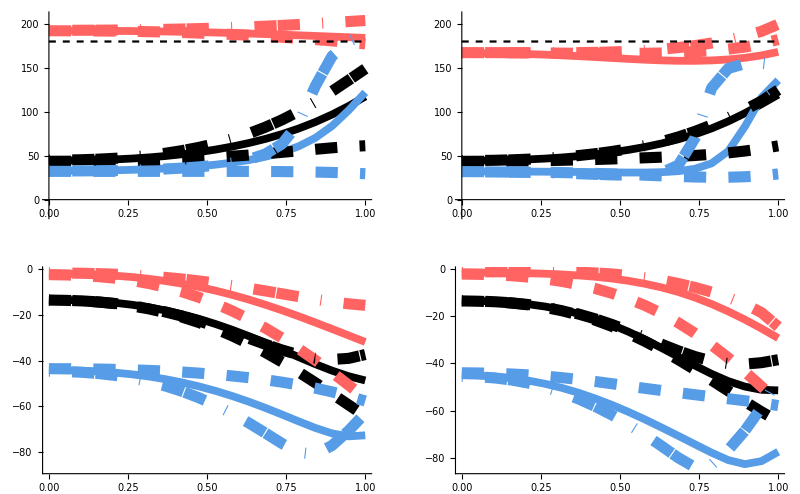

```mathematica
theDATAL={};
phiDATAL={};
theDATAR={};
phiDATAR={};

limbIinit=quatFK[quatsi,lengths,qref]; 
limbIinit=Table[limbIinit[[i]]-limbIinit[[-1]],{i,1,Length[limbIinit]}];

Do[

run=itr2;
fileL=loadFilesL[[run]];
fileR=loadFilesR[[run]];

PNTSiLraw=Import[fileL,"Table"];
PNTSiRraw=Import[fileR,"Table"];

nsamples=Length[PNTSiLraw];

PNTSiL=Table[Partition[PNTSiLraw[[i]],3],{i,1,nsamples}];
PNTSiR=Table[Partition[PNTSiRraw[[i]],3],{i,1,nsamples}];

thefemLdata={};
phifemLdata={};
thefemRdata={};
phifemRdata={};

thetibLdata={};
phitibLdata={};
thetibRdata={};
phitibRdata={};

thetarLdata={};
phitarLdata={};
thetarRdata={};
phitarRdata={};


thepftLdata={};
phipftLdata={};
thepftRdata={};
phipftRdata={};

timeReldata=Table[N@(i-1)/(nsamples-1),{i,1,nsamples}];
Do[
fr=itr;

limbL=PNTSiL[[fr]];
limbR=PNTSiR[[fr]];
limbR=Join[{limbL[[1]]},limbR];
vbodL=limbL[[1]]-limbL[[2]];
vfemL=limbL[[3]]-limbL[[2]];
vtibL=limbL[[3]]-limbL[[4]];
vtarL=limbL[[5]]-limbL[[4]];
vpftL=limbL[[6]]-limbL[[5]];

limbRm=limbR;

stickPlot=Show[
ListPointPlot3D[{{0,0,0}},PlotRange->Table[{-range,range},{i,1,3}],BoxRatios->{1, 1, 1}],
Graphics3D[Line[{limbL,limbRm}]]];


vbodR=limbRm[[1]]-limbRm[[2]];

vfemR=limbRm[[3]]-limbRm[[2]];
vtibR=limbRm[[3]]-limbRm[[4]];
vtarR=limbRm[[5]]-limbRm[[4]];
vpftR=limbRm[[6]]-limbRm[[5]];

t1L=0;t2L=1.0;t3L=-N@Pi/2;(*theta offsets, Left*)
p1L=N@Pi/2;p2L=-1.;p3L=0;(*phi offsets, Left*)

(*order is r, phi, theta*)

thefemL=t1L+t2L*toSpherical[vfemL][[3]]+t3L;
phifemL=p1L+p2L*toSpherical[vfemL][[2]]+p3L;
thefemR=t1L+t2L*toSpherical[vfemR][[3]]+t3L;
phifemR=p1L+p2L*toSpherical[vfemR][[2]]+p3L;

(*<--note negatives for knee*)
thetibL=t1L+t2L*toSpherical[vtibL][[3]]-t3L;
phitibL=-p1L-p2L*toSpherical[vtibL][[2]]+p3L;
thetibR=t1L+t2L*toSpherical[vtibR][[3]]-t3L;
phitibR=-p1L-p2L*toSpherical[vtibR][[2]]+p3L;

thetarL=t1L+t2L*toSpherical[vtarL][[3]]+t3L;
phitarL=p1L+p2L*toSpherical[vtarL][[2]]+p3L;
thetarR=t1L+t2L*toSpherical[vtarR][[3]]+t3L;
phitarR=p1L+p2L*toSpherical[vtarR][[2]]+p3L;

thepftL=t1L+t2L*toSpherical[vpftL][[3]]+t3L;
phipftL=p1L+p2L*toSpherical[vpftL][[2]]+p3L;
thepftR=t1L+t2L*toSpherical[vpftR][[3]]+t3L;
phipftR=p1L+p2L*toSpherical[vpftR][[2]]+p3L;

thefemLdata=Join[thefemLdata,{thefemL}];
phifemLdata=Join[phifemLdata,{phifemL}];
thefemRdata=Join[thefemRdata,{-thefemR}];
phifemRdata=Join[phifemRdata,{phifemR}];

thetibLdata=Join[thetibLdata,{thetibL}];
phitibLdata=Join[phitibLdata,{phitibL}];
thetibRdata=Join[thetibRdata,{thetibR}];
phitibRdata=Join[phitibRdata,{phitibR}];

thetarLdata=Join[thetarLdata,{thetarL}];
phitarLdata=Join[phitarLdata,{phitarL}];
thetarRdata=Join[thetarRdata,{-thetarR}];
phitarRdata=Join[phitarRdata,{phitarR}];

thepftLdata=Join[thepftLdata,{thepftL}];
phipftLdata=Join[phipftLdata,{phipftL}];
thepftRdata=Join[thepftRdata,{thepftR}];
phipftRdata=Join[phipftRdata,{phipftR}];
status={fileL,fileR,itr2,itr};
(*PrintTemporary[stickPlot]*)

,{itr,1,nsamples}];

thefemLdata=1./Degree unwrapPhase@thefemLdata;
phifemLdata=1./Degree unwrapPhase@phifemLdata;
thefemRdata=1./Degree unwrapPhase@thefemRdata;
phifemRdata=1./Degree unwrapPhase@phifemRdata;

thetibLdata=1./Degree unwrapPhase@thetibLdata;
phitibLdata=1./Degree unwrapPhase@phitibLdata;
thetibRdata=1./Degree unwrapPhase@thetibRdata;
phitibRdata=1./Degree unwrapPhase@phitibRdata;

thetarLdata=1./Degree unwrapPhase@thetarLdata;
phitarLdata=1./Degree unwrapPhase@phitarLdata;
thetarRdata=1./Degree unwrapPhase@thetarRdata;
phitarRdata=1./Degree unwrapPhase@phitarRdata;

thepftLdata=1./Degree unwrapPhase@thepftLdata;
phipftLdata=1./Degree unwrapPhase@phipftLdata;
thepftRdata=1./Degree unwrapPhase@thepftRdata;
phipftRdata=1./Degree unwrapPhase@phipftRdata;

thefemLdataXY=Thread[{timeReldata,thefemLdata}];
thetibLdataXY=Thread[{timeReldata,thetibLdata}];
thetarLdataXY=Thread[{timeReldata,thetarLdata}];
thepftLdataXY=Thread[{timeReldata,thepftLdata}];

phifemLdataXY=Thread[{timeReldata,phifemLdata}];
phitibLdataXY=Thread[{timeReldata,phitibLdata}];
phitarLdataXY=Thread[{timeReldata,phitarLdata}];
phipftLdataXY=Thread[{timeReldata,phipftLdata}];

thefemRdataXY=Thread[{timeReldata,thefemRdata}];
thetibRdataXY=Thread[{timeReldata,thetibRdata}];
thetarRdataXY=Thread[{timeReldata,thetarRdata}];
thepftRdataXY=Thread[{timeReldata,thepftRdata}];

phifemRdataXY=Thread[{timeReldata,phifemRdata}];
phitibRdataXY=Thread[{timeReldata,phitibRdata}];
phitarRdataXY=Thread[{timeReldata,phitarRdata}];
phipftRdataXY=Thread[{timeReldata,phipftRdata}];

theDATAL=Join[theDATAL,{{thefemLdataXY,thetibLdataXY,thetarLdataXY,thepftLdataXY}}];
phiDATAL=Join[phiDATAL,{{phifemLdataXY,phitibLdataXY,phitarLdataXY,phipftLdataXY}}];

theDATAR=Join[theDATAR,{{thefemRdataXY,thetibRdataXY,thetarRdataXY,thepftRdataXY}}];
phiDATAR=Join[phiDATAR,{{phifemRdataXY,phitibRdataXY,phitarRdataXY,phipftRdataXY}}];

,{itr2,1,Length[conditionIndices]}]

colorsmod=colors;
colorsmod[[4]]=Transparent;
stylemod=style;
stylemod[[2]]=FontSize->40;
size=800;

dashthickness=0.01;
lineStyles1=Thread[{Thickness[0.007],colorsmod}];
lineStyles2=Thread[{Dashing[0.02],Thickness[dashthickness],colorsmod}];
lineStyles3=Thread[{Dashing[{0.001,0.02,0.02}],Thickness[dashthickness],colorsmod}];
lineStyles5={Black,Dashed};

pA=Show[
ListLinePlot[theDATAL[[1]],PlotStyle->lineStyles1,PlotRange->rangeTheta,BaseStyle->stylemod,AxesStyle->axStyle],
ListLinePlot[theDATAL[[2]],PlotStyle->lineStyles2,PlotRange->All],
ListLinePlot[theDATAL[[3]],PlotStyle->lineStyles3,PlotRange->All],
ListLinePlot[{{0,180},{1,180}},PlotStyle->lineStyles5]
,ImageSize->size];

pC=Show[ListLinePlot[phiDATAL[[1]],PlotStyle->lineStyles1,PlotRange->rangePhi,BaseStyle->stylemod,AxesStyle->axStyle],
ListLinePlot[phiDATAL[[2]],PlotStyle->lineStyles2,PlotRange->rangePhi],
ListLinePlot[phiDATAL[[3]],PlotStyle->lineStyles3,PlotRange->All]
,ImageSize->size];

pB=Show[ListLinePlot[theDATAR[[1]],PlotStyle->lineStyles1,PlotRange->rangeTheta,BaseStyle->stylemod,AxesStyle->axStyle],
ListLinePlot[theDATAR[[2]],PlotStyle->lineStyles2,PlotRange->All],
ListLinePlot[theDATAR[[3]],PlotStyle->lineStyles3,PlotRange->All],
ListLinePlot[{{0,180},{1,180}},PlotStyle->lineStyles5]
,ImageSize->size];

pD=Show[ListLinePlot[phiDATAR[[1]],PlotStyle->lineStyles1,PlotRange->rangePhi,BaseStyle->stylemod,AxesStyle->axStyle],
ListLinePlot[phiDATAR[[2]],PlotStyle->lineStyles2,PlotRange->rangePhi],
ListLinePlot[phiDATAR[[3]],PlotStyle->lineStyles3,PlotRange->All]
,ImageSize->size];

Print["left column: left leg; top row: retraction; bottom: adduction; solid: cond 1; dashed:cond2; dot-dashed:cond3"]
GraphicsGrid[{{pA,pB},{pC,pD}},ImageSize->800]
```

```mathematica
(*save figures as well as information on notebook used to make the figs*)
nbname=(NotebookFileName[]//FileNameSplit)[[-1]];
info="Figures created by "<>nbname;

SetDirectory[setpathfigpanel]
Export["polarAngles_RETL.gif",pA,"TransparentColor"->White];
Export["polarAngles_RETR.gif",pB,"TransparentColor"->White];
Export["polarAngles_ADDL.gif",pC,"TransparentColor"->White];
Export["polarAngles_ADDR.gif",pD,"TransparentColor"->White];
Export["polarAngles_info.txt",info];
ResetDirectory[]
```

/Users/chrisrichards/Desktop/FrogWork/FrogPubs/frogSlerp/figs/panels

/Users/chrisrichards/Desktop/FrogWork/FrogPubs/frogSlerp/simData

## 8. Pick a specific run (from those loaded) and interactively view kinematics R&L legs.

```mathematica
Manipulate[
run=3;
fileL=loadFilesL[[run]];
fileR=loadFilesR[[run]];

PNTSiLraw=Import[fileL,"Table"];
PNTSiRraw=Import[fileR,"Table"];

nsamples=Length[PNTSiLraw];

PNTSiL=Table[Partition[PNTSiLraw[[i]],3],{i,1,nsamples}];
PNTSiR=Table[Partition[PNTSiRraw[[i]],3],{i,1,nsamples}];


limbL=PNTSiL[[fr]];
limbR=PNTSiR[[fr]];
limbR=Join[{limbL[[1]]},limbR];


(*mirror the Right limb just to calculate angles similar to how it was done on left*)
limbRm=limbMirror[limbR,limbR[[2]]-limbR[[1]],{0,0,1},0*limbIinit[[2]]];
limbRm=Table[limbRm[[i]]+2*{1,0,0}*limbIinit[[2]],{i,1,Length[limbRm]}];

vfemL=limbL[[3]]-limbL[[2]];
vtibL=limbL[[3]]-limbL[[4]];
vtarL=limbL[[5]]-limbL[[4]];
vpftL=limbL[[6]]-limbL[[5]];

vfemR=limbRm[[3]]-limbRm[[2]];
vtibR=limbRm[[3]]-limbRm[[4]];
vtarR=limbRm[[5]]-limbRm[[4]];
vpftR=limbRm[[6]]-limbRm[[5]];

segVec=vtibL;

bodyaxis=limbL[[1]]-limbL[[2]];
bodyyaw=VectorAngle[bodyaxis*{1,1,0},{0,1,0}];
bodypitch=Pi/2-VectorAngle[bodyaxis,{0,0,1}];


(*{phi,theta}={N@Pi/2,0}+{-1,1}*CoordinateTransform["Cartesian"->"Spherical",segVec][[2;;]]+{0,-N@Pi/2}; (*for hip*)*)

{phi,theta}={-N@Pi/2,0}+{1,1}*CoordinateTransform["Cartesian"->"Spherical",segVec][[2;;]]+{0,N@Pi/2}; (*for knee*)

(*{phi,theta}={N@Pi/2,0}+{-1,1}*CoordinateTransform["Cartesian"->"Spherical",segVec][[2;;]]+{0,-N@Pi/2}; (*for ankle*)*)

(*{phi,theta}={N@Pi/2,0}+{-1,1}*CoordinateTransform["Cartesian"->"Spherical",segVec][[2;;]]+{0,-N@Pi/2}; (*for tmt*)*)




midframesQ=fr==1(*||fr==nsamples*);
lineThickness=If[midframesQ,0.01,0.0005];
lineColorL=If[midframesQ,Black,Gray];
lineColorR=If[midframesQ,colors[[2]],Pink];
lineColorR=If[run==3,lineColorR,Transparent];(*only show right limb on turn trial*)

FR=IdentityMatrix[3]*0.3;
FR=Riffle[FR,{{0,0,0}}];
FR=Table[FR[[i]]+{-.5,0,0},{i,1,Length[FR]}];

Show[
ListPointPlot3D[limbL,PlotStyle->{Large},PlotRange->Table[
hippnt=PNTSiL[[1,2,i]];
{hippnt-1.1,hippnt+1.1},{i,1,3}],PlotLabel->{bodypitch,bodyyaw},BoxRatios->{1, 1, 1},AxesLabel->{"X","Y","Z"}],
ListPointPlot3D[limbR,PlotStyle->{Large,lineColorR}],
Graphics3D[{lineColorL,Thickness->lineThickness,Line[limbL]}],
Graphics3D[{lineColorR,Thickness->lineThickness,Line[limbR]}],
Graphics3D[{Transparent,Line[limbRm]}],
Graphics3D[{Black,Line[FR[[1;;3]]]}],
Graphics3D[{colors[[2]],Line[FR[[4;;]]]}],
Graphics3D[{Transparent,Line[{{0,0,0},segVec}]}]
,ImageSize->800]
,{fr,1,nsamples,1}]



(*for selecting view point*)
(*Manipulate[
vp={x,y,z};
Show[datasubset,ViewPoint->vp,Boxed->False,Axes->False],{x,-5,5},{y,-5,5},{z,-5,10}]
*)
viewBack={-0.13999999999999968,-5.,-0.1200000000000001};
viewTop={0.,-0.21999999999999975,10.};
view3d={2.5,-3.02,1.8600000000000003};
viewrt={2.7199999999999998,1.2199999999999998,0.};
```

```mathematica
1/Degree 0.281
```

16.1001

```mathematica
animDATA=Table[

run=itr;
fileL=loadFilesL[[run]];
fileR=loadFilesR[[run]];

PNTSiLraw=Import[fileL,"Table"];
PNTSiRraw=Import[fileR,"Table"];

nsamples=Length[PNTSiLraw];

PNTSiL=Table[Partition[PNTSiLraw[[i]],3],{i,1,nsamples}];
PNTSiR=Table[Partition[PNTSiRraw[[i]],3],{i,1,nsamples}];


limbL=PNTSiL[[fr]];
limbR=PNTSiR[[fr]];
limbR=Join[{limbL[[1]]},limbR];


(*mirror the Right limb just to calculate angles similar to how it was done on left*)
limbRm=limbMirror[limbR,limbR[[2]]-limbR[[1]],{0,0,1},0*limbIinit[[2]]];
limbRm=Table[limbRm[[i]]+2*{1,0,0}*limbIinit[[2]],{i,1,Length[limbRm]}];

vfemL=limbL[[3]]-limbL[[2]];
vtibL=limbL[[3]]-limbL[[4]];
vtarL=limbL[[5]]-limbL[[4]];
vpftL=limbL[[6]]-limbL[[5]];

vfemR=limbRm[[3]]-limbRm[[2]];
vtibR=limbRm[[3]]-limbRm[[4]];
vtarR=limbRm[[5]]-limbRm[[4]];
vpftR=limbRm[[6]]-limbRm[[5]];

segVec=vtibL;

bodyaxis=limbL[[1]]-limbL[[2]];
bodyyaw=VectorAngle[bodyaxis*{1,1,0},{0,1,0}];
bodypitch=Pi/2-VectorAngle[bodyaxis,{0,0,1}];


(*{phi,theta}={N@Pi/2,0}+{-1,1}*CoordinateTransform["Cartesian"->"Spherical",segVec][[2;;]]+{0,-N@Pi/2}; (*for hip*)*)

{phi,theta}={-N@Pi/2,0}+{1,1}*CoordinateTransform["Cartesian"->"Spherical",segVec][[2;;]]+{0,N@Pi/2}; (*for knee*)

(*{phi,theta}={N@Pi/2,0}+{-1,1}*CoordinateTransform["Cartesian"->"Spherical",segVec][[2;;]]+{0,-N@Pi/2}; (*for ankle*)*)

(*{phi,theta}={N@Pi/2,0}+{-1,1}*CoordinateTransform["Cartesian"->"Spherical",segVec][[2;;]]+{0,-N@Pi/2}; (*for tmt*)*)




midframesQ=fr==1(*||fr==nsamples*);
lineThickness=If[midframesQ,0.01,0.0005];
lineColorL=If[midframesQ,Black,Gray];
lineColorR=If[midframesQ,colors[[2]],Pink];
lineColorR=If[itr==3,lineColorR,Transparent];(*only show right limb on turn trial*)

FR=IdentityMatrix[3]*0.3;
FR=Riffle[FR,{{0,0,0}}];
FR=Table[FR[[i]]+{-.5,0,0},{i,1,Length[FR]}];

Show[
ListPointPlot3D[limbL,PlotStyle->{Large},PlotRange->Table[
hippnt=PNTSiL[[1,2,i]];
{hippnt-1.1,hippnt+1.1},{i,1,3}],BoxRatios->{1, 1, 1},AxesLabel->{"X","Y","Z"}],
ListPointPlot3D[limbR,PlotStyle->{Large,lineColorR}],
Graphics3D[{lineColorL,Thickness->lineThickness,Line[limbL]}],
Graphics3D[{lineColorR,Thickness->lineThickness,Line[limbR]}],
Graphics3D[{Transparent,Line[limbRm]}],
Graphics3D[{Black,Line[FR[[1;;3]]]}],
Graphics3D[{colors[[2]],Line[FR[[4;;]]]}],
Graphics3D[{Transparent,Line[{{0,0,0},segVec}]}]
,ImageSize->800]
,{fr,1,nsamples},{itr,1,Length[getFiles]}];

Manipulate[
Show[animDATA[[fr]]],{fr,1,Length[animDATA],1}];

(*for selecting view point*)
(*Manipulate[
vp={x,y,z};
Show[datasubset,ViewPoint->vp,Boxed->False,Axes->False],{x,-5,5},{y,-5,5},{z,-5,10}]
*)
viewBack={-0.13999999999999968,-5.,-0.1200000000000001};
viewTop={0.,-0.21999999999999975,10.};
view3d={2.5,-3.02,1.8600000000000003};
viewrt={2.7199999999999998,1.2199999999999998,0.};
```

```mathematica
frameskip=4;

runNum=1;
framelist=Range[1,nframes,frameskip];
framelist=DeleteDuplicates[Join[framelist,{nframes}]];
datasubset=animDATA[[framelist,runNum]];
cond13d=Show[datasubset,ViewPoint->view3d,Boxed->False,Axes->False];
cond1tp=Show[datasubset,ViewPoint->viewTop,Boxed->False,Axes->False];
cond1bk=Show[datasubset,ViewPoint->viewBack,Boxed->False,Axes->False];
cond1rt=Show[datasubset,ViewPoint->viewrt,Boxed->False,Axes->False];

runNum=2;
framelist=Range[1,nframes,frameskip];
framelist=DeleteDuplicates[Join[framelist,{nframes}]];
datasubset=animDATA[[framelist,runNum]];
cond23d=Show[datasubset,ViewPoint->view3d,Boxed->False,Axes->False];
cond2tp=Show[datasubset,ViewPoint->viewTop,Boxed->False,Axes->False];
cond2bk=Show[datasubset,ViewPoint->viewBack,Boxed->False,Axes->False];
cond2rt=Show[datasubset,ViewPoint->viewrt,Boxed->False,Axes->False];

runNum=3;
framelist=Range[1,nframes,frameskip];
framelist=DeleteDuplicates[Join[framelist,{nframes}]];
datasubset=animDATA[[framelist,runNum]];
cond33d=Show[datasubset,ViewPoint->view3d,Boxed->False,Axes->False];
cond3tp=Show[datasubset,ViewPoint->viewTop,Boxed->False,Axes->False];
cond3bk=Show[datasubset,ViewPoint->viewBack,Boxed->False,Axes->False];
cond3rt=Show[datasubset,ViewPoint->viewrt,Boxed->False,Axes->False];
```

```mathematica
(*save figures as well as information on notebook used to make the figs*)
nbname=(NotebookFileName[]//FileNameSplit)[[-1]];
info="Figures created by "<>nbname;

SetDirectory[setpathfigpanel]
Export["stickJumps_cond13d.gif",cond13d,"TransparentColor"->White];
Export["stickJumps_cond23d.gif",cond23d,"TransparentColor"->White];
Export["stickJumps_cond33d.gif",cond33d,"TransparentColor"->White];
Export["stickJumps_cond1tp.gif",cond1tp,"TransparentColor"->White];
Export["stickJumps_cond2tp.gif",cond2tp,"TransparentColor"->White];
Export["stickJumps_cond3tp.gif",cond3tp,"TransparentColor"->White];
Export["stickJumps_cond1bk.gif",cond1bk,"TransparentColor"->White];
Export["stickJumps_cond2bk.gif",cond2bk,"TransparentColor"->White];
Export["stickJumps_cond3bk.gif",cond3bk,"TransparentColor"->White];
Export["stickJumps_cond1rt.gif",cond1rt,"TransparentColor"->White];
Export["stickJumps_cond2rt.gif",cond2rt,"TransparentColor"->White];
Export["stickJumps_cond3rt.gif",cond3rt,"TransparentColor"->White];
Export["stickJumps_info.txt",info];
ResetDirectory[]
```

/Users/chrisrichards/Desktop/FrogWork/FrogPubs/frogSlerp/figs/panels

/Users/chrisrichards/Desktop/FrogWork/FrogPubs/frogSlerp/simData

## 9. Interactively change the target heading of the nominal simulation and watch the kinematic trajectories update. Use for demo. TO DO: - add fig legends for joints

```mathematica
intermediateColor=Setting[0.7722590981918059];(*for intermediate stick figure frames*)
range=1;

pitchlabel=Graphics[Text["Pitch",{0,0},{0,0},{0,1}],BaseStyle->{FontFamily->font,FontSize->Round[fontsizePlot]}];


refframecol=Transparent;
quats1=quatsi;
limbIinit=quatFK[quats1,lengths,qref]; 
limbIinit=Table[limbIinit[[i]]-limbIinit[[-1]],{i,1,Length[limbIinit]}];




Manipulate[
(*change the initial body axis pitch without influencing other segments*)
qpitchInit=aaToq[{1,0,0},pitchangleInit+0*N@Pi/2];
bodyInit=limbIinit[[1]]-limbIinit[[2]];
bodyInitRot=qRot[qpitchInit,bodyInit];
limbInitRot=limbIinit;
limbInitRot[[1]]=limbInitRot[[2]]+bodyInitRot;
quats1mod=limbQUAT[limbInitRot,qref];


quats1=quats1mod;
quats2=quatsfNominal;

qpitch=aaToq[{1,0,0},pitchangle+0*N@Pi/2];
qyaw=aaToq[{0,0,1},yawangle];
qtarget=qMult[qyaw,qpitch];


quats2[[1]]=qMult[qtarget,quats2[[1]]];
(*quats2[[1]]=qtarget;*)

(*-----constrain end of jump based on hip 3d angle--- *)


angHip3d=0;(*hip 3d angle*)
tt=0;(*time value to use*)
dt=0.01;(*increment for time*)
While[angHip3d<130*Pi/180.0(*hip 3d angle threshold*),
quatsItest=limbSlerp[quats1,quats2,tt];
limbItest=quatFK[quatsItest,lengths,qref]; 
limbItest=Table[limbItest[[i]]-limbItest[[-1]],{i,1,Length[limbItest]}];
angHip3d=N@Pi-VectorAngle[limbItest[[1]]-limbItest[[2]],limbItest[[2]]-limbItest[[3]]];
tt=tt+dt;
];

(*scale the timefun according to tt to try to have the same velocity profile*)
timeTable=Table[{time*tt,tt*timefun},{time,0,1,1/(nsamples-1)}];
timefunScaled=Interpolation[timeTable];
(*------------------------------------------------- *)

timevalue=timefunScaled[(tt*t)];

quatsCurr=limbSlerp[quats1,quats2,timevalue];
limbCurr=quatFK[quatsCurr,lengths,qref];
limbCurr=Table[limbCurr[[i]]-limbCurr[[-1]],{i,1,Length[limbCurr]}];

nsticks=5;(*number of stick figures to superimpose*)
limbSticks=Table[
timeStick=timefunScaled[(tt*(tstick-1)/(nsticks-1))];
quatsStick=limbSlerp[quats1,quats2,timeStick];
limbStick=quatFK[quatsStick,lengths,qref];
limbStick=Table[limbStick[[i]]-limbStick[[-1]],{i,1,Length[limbStick]}]
,{tstick,1,nsticks}];

PNTSi=Table[
quatsI=limbSlerp[quats1,quats2,timefunScaled[(tt*relTime)]];
limbI1=quatFK[quatsI,lengths,qref]; 
limbI=Table[limbI1[[i]]-limbI1[[-1]],{i,1,Length[limbI1]}],{relTime,0,1,0.05}];



thefemLdata={};
phifemLdata={};
thefemRdata={};
phifemRdata={};

thetibLdata={};
phitibLdata={};
thetibRdata={};
phitibRdata={};

thetarLdata={};
phitarLdata={};
thetarRdata={};
phitarRdata={};


thepftLdata={};
phipftLdata={};
thepftRdata={};
phipftRdata={};

Do[
limbL=PNTSi[[i]];
vbodL=limbL[[1]]-limbL[[2]];
vfemL=limbL[[3]]-limbL[[2]];
vtibL=limbL[[3]]-limbL[[4]];
vtarL=limbL[[5]]-limbL[[4]];
vpftL=limbL[[6]]-limbL[[5]];

t1L=0;t2L=1.0;t3L=-N@Pi/2;(*theta offsets, Left*)
p1L=N@Pi/2;p2L=-1.;p3L=0;(*phi offsets, Left*)

(*order is r, phi, theta*)

thefemL=t1L+t2L*toSpherical[vfemL][[3]]+t3L;
phifemL=p1L+p2L*toSpherical[vfemL][[2]]+p3L;

(*<--note negatives for knee*)
thetibL=t1L+t2L*toSpherical[vtibL][[3]]-t3L;
phitibL=-p1L-p2L*toSpherical[vtibL][[2]]+p3L;

thetarL=t1L+t2L*toSpherical[vtarL][[3]]+t3L;
phitarL=p1L+p2L*toSpherical[vtarL][[2]]+p3L;

thepftL=t1L+t2L*toSpherical[vpftL][[3]]+t3L;
phipftL=p1L+p2L*toSpherical[vpftL][[2]]+p3L;

thefemLdata=Join[thefemLdata,{thefemL}];
phifemLdata=Join[phifemLdata,{phifemL}];

thetibLdata=Join[thetibLdata,{thetibL}];
phitibLdata=Join[phitibLdata,{phitibL}];

thetarLdata=Join[thetarLdata,{thetarL}];
phitarLdata=Join[phitarLdata,{phitarL}];

thepftLdata=Join[thepftLdata,{thepftL}];
phipftLdata=Join[phipftLdata,{phipftL}];

,{i,1,Length[PNTSi]}];

thefemLdata=1./Degree  unwrapPhase@thefemLdata;
phifemLdata=1./Degree  unwrapPhase@phifemLdata;

thetibLdata=1./Degree  unwrapPhase@thetibLdata;
phitibLdata=1./Degree  unwrapPhase@phitibLdata;

thetarLdata=1./Degree  unwrapPhase@thetarLdata;
phitarLdata=1./Degree  unwrapPhase@phitarLdata;

thepftLdata=1./Degree  unwrapPhase@thepftLdata;
phipftLdata=1./Degree  unwrapPhase@phipftLdata;

ndat=Length[phifemLdata];
datTimeValues=Table[N@(i-1)/(ndat-1),{i,1,ndat}];

thefemLdataXY=Thread[{datTimeValues,thefemLdata}];
phifemLdataXY=Thread[{datTimeValues,phifemLdata}];

thetibLdataXY=Thread[{datTimeValues,thetibLdata}];
phitibLdataXY=Thread[{datTimeValues,phitibLdata}];

thetarLdataXY=Thread[{datTimeValues,thetarLdata}];
phitarLdataXY=Thread[{datTimeValues,phitarLdata}];

thepftLdataXY=Thread[{datTimeValues,thepftLdata}];
phipftLdataXY=Thread[{datTimeValues,phipftLdata}];

bodyaxis=limbL[[1]]-limbL[[2]];
bodyyaw=VectorAngle[bodyaxis*{1,1,0},{0,1,0}];
bodypitch=Pi/2-VectorAngle[bodyaxis,{0,0,1}];

label="Takeoff pitch = "<>ToString[Round[180*bodypitch/3.14]]<>" deg \n"<>"Takeoff yaw = "<>ToString[Round[180*bodyyaw/3.14]]<>" deg \n";

P1=Show[
ListPointPlot3D[limbCurr,PlotRange->Table[{-range,range},{i,1,3}],BoxRatios->{1, 1, 1},PlotLabel->label(*,AxesLabel->{"X","Y","Z"}*),Boxed->False,Axes->{True,True,False},Ticks->False,BaseStyle->style],
Graphics3D[{Thick,Line[limbCurr]}],
Graphics3D[{Thin,intermediateColor,Line[limbSticks]}]



,ViewPoint->{Top,{1,-2,1},Front}[[3]],ViewCenter->Automatic];

P1a=Show[
ListPointPlot3D[limbCurr,PlotRange->Table[{-range,range},{i,1,3}],BoxRatios->{1, 1, 1},PlotLabel->label,(*AxesLabel->{"X","Y","Z"},*)Boxed->False,Axes->{False,True,True},Ticks->False,BaseStyle->style],
Graphics3D[{Thick,Line[limbCurr]}],
Graphics3D[{Thin,intermediateColor,Line[limbSticks]}],
Graphics3D[{Gray,Dashed,Line[{{0,ymarker,0},{0,ymarker,2}}]}]


,ViewPoint->Right,ViewCenter->Automatic];

P2=Show[
ListLinePlot[{thefemLdataXY,thetibLdataXY,thetarLdataXY,thepftLdataXY},PlotStyle->{{Thick,colors[[1]]},{Thick,colors[[2]]},{Thick,colors[[3]]},{Thick,colors[[4]]}},PlotRange->rangeTheta,BaseStyle->style,AxesStyle->axStyle],
p2line=ListLinePlot[{{t,0},{t,rangeTheta[[2,2]]}},PlotStyle->{Thick,Dashed,Black}]
];

P3=Show[
ListLinePlot[{phifemLdataXY,phitibLdataXY,phitarLdataXY,phipftLdataXY},PlotStyle->{{Thick,colors[[1]]},{Thick,colors[[2]]},{Thick,colors[[3]]},{Thick,colors[[4]]}},PlotRange->rangePhi,BaseStyle->style,AxesStyle->axStyle],
p3line=ListLinePlot[{{t,rangePhi[[2,2]]},{t,0}},PlotStyle->{Thick,Dashed,Black}]
];

(*---for sliders-----*)
slidersize=100;

sliderfraction=0.6;(*fraction of slider within slider inset*)
targetSlider=Plot[blank,{blank,0,1},PlotStyle->Transparent,Axes->False,AspectRatio->1,Epilog->{
Inset[Slider2D[{-yawangle,pitchangle},{-2,2},ImageSize->{sliderfraction*slidersize,sliderfraction*slidersize}]],
Inset["Yaw",Scaled[{0.53,0.9}],Scaled[{0.5,0.5}]],
Inset[pitchlabel,Scaled[{0.1,0.53}],Scaled[{0.5,0.5}]]

},ImageSize->{slidersize,slidersize},BaseStyle->style];

timeSlider=Plot[blank,{blank,0,1},PlotStyle->Transparent,Axes->False,AspectRatio->1,Epilog->{
Inset[Slider[Round[t,0.01],{0,1},Appearance->"Labeled",BaseStyle->style],Scaled[{0.5,0.5}],Scaled[{0.5,0.5}]],
Inset["τ",Scaled[{0.35,0.505}],Scaled[{0.5,0.5}]]

},ImageSize->{10slidersize,10slidersize},BaseStyle->style];

(*-------------------*)


GraphicsGrid[{{P1,P1a},{P2,P3}},ImageSize->700,Epilog->{
Inset["Relative time (τ)",Scaled[{0.55,-0.3}],Scaled[{0.5,0.5}]],
Inset["X",Scaled[{0,0.58}],Scaled[{0.5,0.5}]],
Inset["Y",Scaled[{-0.3,0.9}],Scaled[{0.5,0.5}]],
Inset["Y",Scaled[{1,0.58}],Scaled[{0.5,0.5}]],
Inset["Z",Scaled[{0.67,0.9}],Scaled[{0.5,0.5}]],
Inset["Segment retraction angle(°)\nhip 3D angle"<>ToString[1./Degree VectorAngle[vbodL,vfemL]],Scaled[{0,0.35}],Scaled[{0.5,0.5}]],
Inset["Segment adduction angle(°)",Scaled[{1,0.35}],Scaled[{0.5,0.5}]],
Inset[timeSlider,Scaled[{0.55,0.47}],Scaled[{0.5,0.5}]],
Inset[targetSlider,Scaled[{0.47,0.7}],Scaled[{0.5,0.5}]]
},BaseStyle->style,Spacings->{0,Scaled[.5]}]

,{t,0,1},{{pitchangle,0},-2,4},{{yawangle,0},-2,2},{{pitchangleInit,0},-2,2},{{ymarker,0},-2,2},TrackedSymbols->{t,pitchangle,yawangle,pitchangleInit,ymarker}]
```

```mathematica
quats1
```

{{-0.363724,0.931507,1.53208×10^-16,2.58043×10^-16},{0.425554,0.44695,0.191102,-0.763295},{0.287463,-0.389304,-0.105053,0.868776},{0.406053,0.840938,0.193211,-0.30102},{0.874485,0.385216,-0.07552,-0.284923}}

## 10. Make the above into a demo video simulating user control playing with the values

```mathematica
nsteps=10;
nconds=12;(*how many conditinos*)
stepLengths=Table[nsteps,{i,1,nconds}];(*how many steps to do through each change of condition*)

pauseLengths=Table[2,{i,1,nconds}];(*length of pauses between condition*)
npauses=Length[pauseLengths];(*number of pauses*)
nslices=nconds+npauses;
sliceLengths=Riffle[stepLengths,pauseLengths];
nindices=Total[sliceLengths];
(*number of indices which will become slices for simulated user data*)
sliceData=Range[1,nindices];
slices=listSplit[sliceData,sliceLengths];

(*---generate simulated user control data to operate sliders---*)

(*maxpitch=1;maxyaw=0.47;minpitch=-0.7;*)
maxpitch=1;maxyaw=0.51;minpitch=-0.52;
(*slider control data for time, yaw, pitch*)
timeData=yawData=pitchData=Table[0,{i,1,nindices}];

timeup=Table[N@(i-1)/(nsteps-1),{i,1,nsteps}];
timedown=Table[1-N@(i-1)/(nsteps-1),{i,1,nsteps}];
pitchup=Table[maxpitch*N@(i-1)/(nsteps-1),{i,1,nsteps}];
pitchdown=pitchdown=Table[-((maxpitch-minpitch)N@(i-1)/(nsteps-1))+maxpitch,{i,1,nsteps}];
yawup=Table[maxyaw*N@(i-1)/(nsteps-1),{i,1,nsteps}];
yawdown=maxyaw-yawup;
pitchreset=timedown*minpitch;
yawreset=maxyaw*timedown;

(*-------GENERATE SIMULATEED USER DATA-------*)

slice=slices[[1]];
timeData[[slice]]=timeup;
pitchData[[slice]]=0;
yawData[[slice]]=0;

slice=slices[[2]];
timeData[[slice]]=1;
pitchData[[slice]]=0;
yawData[[slice]]=0;

slice=slices[[3]];
timeData[[slice]]=timedown;
pitchData[[slice]]=0;
yawData[[slice]]=0;

slice=slices[[4]];
timeData[[slice]]=0;
pitchData[[slice]]=0;
yawData[[slice]]=0;

slice=slices[[5]];
timeData[[slice]]=0;
pitchData[[slice]]=pitchup;
yawData[[slice]]=0;

slice=slices[[6]];
timeData[[slice]]=0;
pitchData[[slice]]=maxpitch;
yawData[[slice]]=0;

slice=slices[[7]];
timeData[[slice]]=timeup;
pitchData[[slice]]=maxpitch;
yawData[[slice]]=0;

slice=slices[[8]];
timeData[[slice]]=1;
pitchData[[slice]]=maxpitch;
yawData[[slice]]=0;

slice=slices[[9]];
timeData[[slice]]=timedown;
pitchData[[slice]]=maxpitch;
yawData[[slice]]=0;

slice=slices[[10]];
timeData[[slice]]=0;
pitchData[[slice]]=maxpitch;
yawData[[slice]]=0;

slice=slices[[11]];
timeData[[slice]]=0;
pitchData[[slice]]=pitchdown;
yawData[[slice]]=0;

slice=slices[[12]];
timeData[[slice]]=0;
pitchData[[slice]]=minpitch;
yawData[[slice]]=0;

slice=slices[[13]];
timeData[[slice]]=timeup;
pitchData[[slice]]=minpitch;
yawData[[slice]]=0;

slice=slices[[14]];
timeData[[slice]]=1;
pitchData[[slice]]=minpitch;
yawData[[slice]]=0;

slice=slices[[15]];
timeData[[slice]]=timedown;
pitchData[[slice]]=minpitch;
yawData[[slice]]=0;

slice=slices[[16]];
timeData[[slice]]=0;
pitchData[[slice]]=minpitch;
yawData[[slice]]=0;

slice=slices[[17]];
timeData[[slice]]=0;
pitchData[[slice]]=minpitch;
yawData[[slice]]=yawup;

slice=slices[[18]];
timeData[[slice]]=0;
pitchData[[slice]]=minpitch;
yawData[[slice]]=maxyaw;

slice=slices[[19]];
timeData[[slice]]=timeup;
pitchData[[slice]]=minpitch;
yawData[[slice]]=maxyaw;

slice=slices[[20]];
timeData[[slice]]=1;
pitchData[[slice]]=minpitch;
yawData[[slice]]=maxyaw;

slice=slices[[21]];
timeData[[slice]]=timedown;
pitchData[[slice]]=minpitch;
yawData[[slice]]=maxyaw;

slice=slices[[22]];
timeData[[slice]]=0;
pitchData[[slice]]=minpitch;
yawData[[slice]]=maxyaw;

slice=slices[[23]];
timeData[[slice]]=0;
pitchData[[slice]]=pitchreset;
yawData[[slice]]=yawreset;

slice=slices[[24]];
timeData[[slice]]=0;
pitchData[[slice]]=0;
yawData[[slice]]=0;
```

```mathematica
(*-------CREATE ANIMATION-------*)

intermediateColor=Setting[0.7722590981918059];(*for intermediate stick figure frames*)
range=1;

pitchlabel=Graphics[Text["Pitch",{0,0},{0,0},{0,1}],BaseStyle->{FontFamily->font,FontSize->Round[fontsizePlot]}];


refframecol=Transparent;
quats1=quatsi;
limbIinit=quatFK[quats1,lengths,qref]; 
limbIinit=Table[limbIinit[[i]]-limbIinit[[-1]],{i,1,Length[limbIinit]}];


animation=Table[
t=timeData[[frame]];
pitchangle=pitchData[[frame]];
yawangle=yawData[[frame]];
quats2=quatsfNominal;
qpitch=aaToq[{1,0,0},pitchangle+0*N@Pi/2];
qyaw=aaToq[{0,0,1},yawangle];
qtarget=qMult[qyaw,qpitch];
quats2[[1]]=qMult[qtarget,quats2[[1]]];
(*quats2[[1]]=qtarget;*)

(*-----constrain end of jump based on hip 3d angle--- *)


angHip3d=0;(*hip 3d angle*)
tt=0;(*time value to use*)
dt=0.01;(*increment for time*)
While[angHip3d<130*Pi/180.0(*hip 3d angle threshold*),
quatsItest=limbSlerp[quats1,quats2,tt];
limbItest=quatFK[quatsItest,lengths,qref]; 
limbItest=Table[limbItest[[i]]-limbItest[[-1]],{i,1,Length[limbItest]}];
angHip3d=N@Pi-VectorAngle[limbItest[[1]]-limbItest[[2]],limbItest[[2]]-limbItest[[3]]];
tt=tt+dt;
];

(*scale the timefun according to tt to try to have the same velocity profile*)
timeTable=Table[{time*tt,tt*timefun},{time,0,1,1/(nsamples-1)}];
timefunScaled=Interpolation[timeTable];
(*------------------------------------------------- *)

timevalue=timefunScaled[(tt*t)];

quatsCurr=limbSlerp[quats1,quats2,timevalue];
limbCurr=quatFK[quatsCurr,lengths,qref];
limbCurr=Table[limbCurr[[i]]-limbCurr[[-1]],{i,1,Length[limbCurr]}];

nsticks=8;(*number of stick figures to superimpose*)
limbSticks=Table[
timeStick=timefunScaled[(tt*(tstick-1)/(nsticks-1))];
quatsStick=limbSlerp[quats1,quats2,timeStick];
limbStick=quatFK[quatsStick,lengths,qref];
limbStick=Table[limbStick[[i]]-limbStick[[-1]],{i,1,Length[limbStick]}]
,{tstick,1,nsticks}];

PNTSi=Table[
quatsI=limbSlerp[quats1,quats2,timefunScaled[(tt*relTime)]];
limbI1=quatFK[quatsI,lengths,qref]; 
limbI=Table[limbI1[[i]]-limbI1[[-1]],{i,1,Length[limbI1]}],{relTime,0,1,0.05}];



thefemLdata={};
phifemLdata={};
thefemRdata={};
phifemRdata={};

thetibLdata={};
phitibLdata={};
thetibRdata={};
phitibRdata={};

thetarLdata={};
phitarLdata={};
thetarRdata={};
phitarRdata={};


thepftLdata={};
phipftLdata={};
thepftRdata={};
phipftRdata={};

Do[
limbL=PNTSi[[i]];
vbodL=limbL[[1]]-limbL[[2]];
vfemL=limbL[[3]]-limbL[[2]];
vtibL=limbL[[3]]-limbL[[4]];
vtarL=limbL[[5]]-limbL[[4]];
vpftL=limbL[[6]]-limbL[[5]];

t1L=0;t2L=1.0;t3L=-N@Pi/2;(*theta offsets, Left*)
p1L=N@Pi/2;p2L=-1.;p3L=0;(*phi offsets, Left*)

(*order is r, phi, theta*)

thefemL=t1L+t2L*toSpherical[vfemL][[3]]+t3L;
phifemL=p1L+p2L*toSpherical[vfemL][[2]]+p3L;

(*<--note negatives for knee*)
thetibL=t1L+t2L*toSpherical[vtibL][[3]]-t3L;
phitibL=-p1L-p2L*toSpherical[vtibL][[2]]+p3L;

thetarL=t1L+t2L*toSpherical[vtarL][[3]]+t3L;
phitarL=p1L+p2L*toSpherical[vtarL][[2]]+p3L;

thepftL=t1L+t2L*toSpherical[vpftL][[3]]+t3L;
phipftL=p1L+p2L*toSpherical[vpftL][[2]]+p3L;

thefemLdata=Join[thefemLdata,{thefemL}];
phifemLdata=Join[phifemLdata,{phifemL}];

thetibLdata=Join[thetibLdata,{thetibL}];
phitibLdata=Join[phitibLdata,{phitibL}];

thetarLdata=Join[thetarLdata,{thetarL}];
phitarLdata=Join[phitarLdata,{phitarL}];

thepftLdata=Join[thepftLdata,{thepftL}];
phipftLdata=Join[phipftLdata,{phipftL}];

,{i,1,Length[PNTSi]}];

thefemLdata=1./Degree  unwrapPhase@thefemLdata;
phifemLdata=1./Degree  unwrapPhase@phifemLdata;

thetibLdata=1./Degree  unwrapPhase@thetibLdata;
phitibLdata=1./Degree  unwrapPhase@phitibLdata;

thetarLdata=1./Degree  unwrapPhase@thetarLdata;
phitarLdata=1./Degree  unwrapPhase@phitarLdata;

thepftLdata=1./Degree  unwrapPhase@thepftLdata;
phipftLdata=1./Degree  unwrapPhase@phipftLdata;

ndat=Length[phifemLdata];
datTimeValues=Table[N@(i-1)/(ndat-1),{i,1,ndat}];

thefemLdataXY=Thread[{datTimeValues,thefemLdata}];
phifemLdataXY=Thread[{datTimeValues,phifemLdata}];

thetibLdataXY=Thread[{datTimeValues,thetibLdata}];
phitibLdataXY=Thread[{datTimeValues,phitibLdata}];

thetarLdataXY=Thread[{datTimeValues,thetarLdata}];
phitarLdataXY=Thread[{datTimeValues,phitarLdata}];

thepftLdataXY=Thread[{datTimeValues,thepftLdata}];
phipftLdataXY=Thread[{datTimeValues,phipftLdata}];

bodyaxis=limbL[[1]]-limbL[[2]];
bodyyaw=VectorAngle[bodyaxis*{1,1,0},{0,1,0}];
bodypitch=Pi/2-VectorAngle[bodyaxis,{0,0,1}];

label="Takeoff pitch = "<>ToString[Round[180*bodypitch/3.14]]<>" deg \n"<>"Takeoff yaw = "<>ToString[Round[180*bodyyaw/3.14]]<>" deg \n";

P1=Show[
ListPointPlot3D[limbCurr,PlotRange->Table[{-range,range},{i,1,3}],BoxRatios->{1, 1, 1},PlotLabel->label(*,AxesLabel->{"X","Y","Z"}*),Boxed->False,Axes->{True,True,False},Ticks->False,BaseStyle->style],
Graphics3D[{Thick,Line[limbCurr]}],
Graphics3D[{Thin,intermediateColor,Line[limbSticks]}]



,ViewPoint->{Top,{1,-2,1},Front}[[1]],ViewCenter->Automatic];

P1a=Show[
ListPointPlot3D[limbCurr,PlotRange->Table[{-range,range},{i,1,3}],BoxRatios->{1, 1, 1},PlotLabel->label,(*AxesLabel->{"X","Y","Z"},*)Boxed->False,Axes->{False,True,True},Ticks->False,BaseStyle->style],
Graphics3D[{Thick,Line[limbCurr]}],
Graphics3D[{Thin,intermediateColor,Line[limbSticks]}]

,ViewPoint->Right,ViewCenter->Automatic];

P2=Show[
ListLinePlot[{thefemLdataXY,thetibLdataXY,thetarLdataXY,thepftLdataXY},PlotStyle->{{Thick,colors[[1]]},{Thick,colors[[2]]},{Thick,colors[[3]]},{Thick,Transparent(*colors[[4]]*)}},PlotRange->rangeTheta,BaseStyle->style,AxesStyle->axStyle],
p2line=ListLinePlot[{{t,0},{t,rangeTheta[[2,2]]}},PlotStyle->{Thick,Dashed,Black}]
];

P3=Show[
ListLinePlot[{phifemLdataXY,phitibLdataXY,phitarLdataXY,phipftLdataXY},PlotStyle->{{Thick,colors[[1]]},{Thick,colors[[2]]},{Thick,colors[[3]]},{Thick,Transparent(*colors[[4]]*)}},PlotRange->rangePhi,BaseStyle->style,AxesStyle->axStyle],
p3line=ListLinePlot[{{t,rangePhi[[2,2]]},{t,0}},PlotStyle->{Thick,Dashed,Black}]
];

(*---for sliders-----*)
slidersize=100;

sliderfraction=0.6;(*fraction of slider within slider inset*)
targetSlider=Plot[blank,{blank,0,1},PlotStyle->Transparent,Axes->False,AspectRatio->1,Epilog->{
Inset[Slider2D[{-yawangle,pitchangle},{-2,2},ImageSize->{sliderfraction*slidersize,sliderfraction*slidersize}]],
Inset["Yaw",Scaled[{0.53,0.9}],Scaled[{0.5,0.5}]],
Inset[pitchlabel,Scaled[{0.1,0.53}],Scaled[{0.5,0.5}]]

},ImageSize->{slidersize,slidersize},BaseStyle->style];

timeSlider=Plot[blank,{blank,0,1},PlotStyle->Transparent,Axes->False,AspectRatio->1,Epilog->{
Inset[Slider[Round[t,0.01],{0,1},Appearance->"Labeled",BaseStyle->style],Scaled[{0.5,0.5}],Scaled[{0.5,0.5}]],
Inset["τ",Scaled[{0.35,0.505}],Scaled[{0.5,0.5}]]

},ImageSize->{10slidersize,10slidersize},BaseStyle->style];

(*-------------------*)

status={frame,nindices};

GraphicsGrid[{{P1,P1a},{P2,P3}},ImageSize->700,Epilog->{
Inset["Relative time (τ)",Scaled[{0.55,-0.3}],Scaled[{0.5,0.5}]],
Inset["X",Scaled[{0,0.58}],Scaled[{0.5,0.5}]],
Inset["Y",Scaled[{-0.3,0.9}],Scaled[{0.5,0.5}]],
Inset["Y",Scaled[{1,0.58}],Scaled[{0.5,0.5}]],
Inset["Z",Scaled[{0.67,0.9}],Scaled[{0.5,0.5}]],
Inset["Segment retraction angle(°)",Scaled[{0,0.35}],Scaled[{0.5,0.5}]],
Inset["Segment adduction angle(°)",Scaled[{1,0.35}],Scaled[{0.5,0.5}]],
Inset[timeSlider,Scaled[{0.55,0.47}],Scaled[{0.5,0.5}]],
Inset[targetSlider,Scaled[{0.47,0.7}],Scaled[{0.5,0.5}]]
},BaseStyle->style,Spacings->{0,Scaled[.5]}]

,{frame,1,nindices}];
```

```mathematica
Manipulate[animation[[fr]],{fr,1,Length[animation],1}]
```

```mathematica
Dynamic[status]
```

```mathematica
(*Export to ms folder*)
SetDirectory[setpathms]
Export["SIMovie1.mov",animation,"FrameRate"->5]
ResetDirectory[]
```

/Users/chrisrichards/Desktop/FrogWork/FrogPubs/frogSlerp

SIMovie1.mov

/Users/chrisrichards/Desktop/FrogWork/FrogPubs/frogSlerp/simData

```mathematica
(*save figures as well as information on notebook used to make the figs*)
nbname=(NotebookFileName[]//FileNameSplit)[[-1]];
info="Figures created by "<>nbname;
SetDirectory[setpathfigpanel]
Export["linearVsNonlinearA.pdf",panelA];
Export["linearVsNonlinearA_info.txt",info];
ResetDirectory[]
```

## 11. Vary pitch and yaw target angles from reference configuration

```mathematica
finalAngles={{0.574,0},{1.03,0},{0.258,0.31}};(*pitch and yaw takeoff angles for 3 conditions use for the figures*)
finalAngles*1/Degree
```

{{32.8878,0},{59.0147,0},{14.7823,17.7617}}

```mathematica
(*---SELECT PITCH or YAW modulation*)
pitchORyaw=1;(*1 for pitch, 2 for yaw, 3 for varying init angle and compensating pitch so final angle is 60'*)

femRETminData={};
femRETmaxData={};
femRETexcData={};
tibRETminData={};
tibRETmaxData={};
tibRETexcData={};
tarRETminData={};
tarRETmaxData={};
tarRETexcData={};
pftRETminData={};
pftRETmaxData={};
pftRETexcData={};

femADDminData={};
femADDmaxData={};
femADDexcData={};
tibADDminData={};
tibADDmaxData={};
tibADDexcData={};
tarADDminData={};
tarADDmaxData={};
tarADDexcData={};
pftADDminData={};
pftADDmaxData={};
pftADDexcData={};

hipexcData={};
kneexcData={};
ankexcData={};
tmtexcData={};

hipexc4dData={};
kneexc4dData={};
ankexc4dData={};
tmtexc4dData={};

vcomAnglesTakeoff={};
prepAngleData={};

angData={};
pitchData={};

stickPlotsInit={};

quats1=quatsi;
limbIinit=quatFK[quats1,lengths,qref]; 
limbIinit=Table[limbIinit[[i]]-limbIinit[[-1]],{i,1,Length[limbIinit]}];

ndata={20,20,10}[[pitchORyaw]];(*number of incremental target angles to consider*)
maxpitch=1;maxyaw=0.47;minpitch=-0.7;minyaw=-0.47;
pitchup=Table[-((maxpitch-minpitch)N@(i-1)/(ndata-1))+maxpitch,{i,1,ndata}]//Reverse;
yawup=Table[-((maxyaw-minyaw)N@(i-1)/(ndata-1))+maxyaw,{i,1,ndata}]//Reverse;

(*for initial pitch*)
minpitchInit=-0.27;
maxpitchInit=1.0;
nsteps=10;
pitchInitup=Table[-((maxpitchInit-minpitchInit)N@(i-1)/(nsteps-1))+maxpitchInit,{i,1,nsteps}]//Reverse;
pitchAnglesComp={2.45,1.4,0.95,0.8,0.66,0.54,0.45,0.33,0.2,0.02};(*compensating pitch angles so that takeoff always = 60 deg*)
pitchInitup=Join[pitchInitup,Table[0,{i,1,10}]];
pitchAnglesComp=Join[pitchAnglesComp,Table[0,{i,1,10}]];

Do[
(*Manipulate[*)
pitchAngInit={0,0,pitchInitup[[itr]]}[[pitchORyaw]];
pitchAng={pitchup[[itr]],minpitch,pitchAnglesComp[[itr]]}[[pitchORyaw]];
yawAng={0,yawup[[itr]],0}[[pitchORyaw]];


(*change the initial body axis pitch without influencing other segments*)
qpitchInit=aaToq[{1,0,0},pitchAngInit+0*N@Pi/2];
bodyInit=limbIinit[[1]]-limbIinit[[2]];
bodyInitRot=qRot[qpitchInit,bodyInit];
limbInitRot=limbIinit;
limbInitRot[[1]]=limbInitRot[[2]]+bodyInitRot;
quats1mod=limbQUAT[limbInitRot,qref];


quats1=quats1mod;


quats2=quatsfNominal;
qpitch=aaToq[{1,0,0},pitchAng+0*N@Pi/2];
qyaw=aaToq[{0,0,1},yawAng];
qtarget=qMult[qyaw,qpitch];
quats2[[1]]=qMult[qtarget,quats2[[1]]];
(*quats2[[1]]=qtarget;*)

(*-----constrain end of jump based on hip 3d angle--- *)


angHip3d=0;(*hip 3d angle*)
tt=0;(*time value to use*)
dt=0.01;(*increment for time*)
While[angHip3d<130*Pi/180.0(*hip 3d angle threshold*),
quatsItest=limbSlerp[quats1,quats2,tt];
limbItest=quatFK[quatsItest,lengths,qref]; 
limbItest=Table[limbItest[[i]]-limbItest[[-1]],{i,1,Length[limbItest]}];
angHip3d=N@Pi-VectorAngle[limbItest[[1]]-limbItest[[2]],limbItest[[2]]-limbItest[[3]]];
tt=tt+dt;
];

(*scale the timefun according to tt to try to have the same velocity profile*)
timeTable=Table[{time*tt,tt*timefun},{time,0,1,1/(nsamples-1)}];
timefunScaled=Interpolation[timeTable];

npoints=50;(*number of points to make graphs*)
PNTSi=Table[
quatsI=limbSlerp[quats1,quats2,timefunScaled[(tt*relTime)]];
limbI1=quatFK[quatsI,lengths,qref]; 
limbI=Table[limbI1[[i]]-limbI1[[-1]],{i,1,Length[limbI1]}],{relTime,0,1,1.0/(npoints-1)}];

stickPlot=Show[
ListPointPlot3D[{{0,0,0}},PlotRange->Table[{-range,range},{i,1,3}],BoxRatios->{1, 1, 1}],
Graphics3D[Line[PNTSi[[1;;-1;;5]]]]];

thefemLdata={};
phifemLdata={};
thefemRdata={};
phifemRdata={};

thetibLdata={};
phitibLdata={};
thetibRdata={};
phitibRdata={};

thetarLdata={};
phitarLdata={};
thetarRdata={};
phitarRdata={};


thepftLdata={};
phipftLdata={};
thepftRdata={};
phipftRdata={};

hipAng3dData={};
kneAng3dData={};
ankAng3dData={};
tmtAng3dData={};

hipAng4dData={};
kneAng4dData={};
ankAng4dData={};
tmtAng4dData={};

comXdata={};
comYdata={};
comZdata={};

Do[
limbL=PNTSi[[i]];
vbodL=limbL[[1]]-limbL[[2]];
vfemL=limbL[[3]]-limbL[[2]];
vtibL=limbL[[3]]-limbL[[4]];
vtarL=limbL[[5]]-limbL[[4]];
vpftL=limbL[[6]]-limbL[[5]];

bodyaxis=limbL[[1]]-limbL[[2]];
bodyyaw=-VectorAngle[bodyaxis*{1,1,0},{0,1,0}]*Sign[yawAng];
bodypitch=Pi/2-VectorAngle[bodyaxis,{0,0,1}];

t1L=0;t2L=1.0;t3L=-N@Pi/2;(*theta offsets, Left*)
p1L=N@Pi/2;p2L=-1.;p3L=0;(*phi offsets, Left*)

(*------------3D ANGLES--------------*)
hipAng3d=VectorAngle[vbodL,vfemL];
kneAng3d=VectorAngle[vfemL,vtibL];
ankAng3d=VectorAngle[vtibL,vtarL];
tmtAng3d=VectorAngle[vtarL,vpftL];
(*----------------------------------*)

(*-----------4D ANGLES--------------*)
quatsL=limbQUAT[limbL,qref];
angles4d=Table[VectorAngle[quatsL[[i]],quatsL[[i+1]]],{i,1,Length[quatsL]-1}];


(*-----------------------------------*)

(*---com data----*)
comXdata=Join[comXdata,{limbL[[2,1]]}];
comYdata=Join[comYdata,{limbL[[2,2]]}];
comZdata=Join[comZdata,{limbL[[2,3]]}];
(*order is r, phi, theta*)

thefemL=t1L+t2L*toSpherical[vfemL][[3]]+t3L;
phifemL=p1L+p2L*toSpherical[vfemL][[2]]+p3L;

(*<--note negatives for knee*)
thetibL=t1L+t2L*toSpherical[vtibL][[3]]-t3L;
phitibL=-p1L-p2L*toSpherical[vtibL][[2]]+p3L;

thetarL=t1L+t2L*toSpherical[vtarL][[3]]+t3L;
phitarL=p1L+p2L*toSpherical[vtarL][[2]]+p3L;

thepftL=t1L+t2L*toSpherical[vpftL][[3]]+t3L;
phipftL=p1L+p2L*toSpherical[vpftL][[2]]+p3L;

thefemLdata=Join[thefemLdata,{thefemL}];
phifemLdata=Join[phifemLdata,{phifemL}];

thetibLdata=Join[thetibLdata,{thetibL}];
phitibLdata=Join[phitibLdata,{phitibL}];

thetarLdata=Join[thetarLdata,{thetarL}];
phitarLdata=Join[phitarLdata,{phitarL}];

thepftLdata=Join[thepftLdata,{thepftL}];
phipftLdata=Join[phipftLdata,{phipftL}];

hipAng3dData=Join[hipAng3dData,{hipAng3d}];
kneAng3dData=Join[kneAng3dData,{kneAng3d}];
ankAng3dData=Join[ankAng3dData,{ankAng3d}];
tmtAng3dData=Join[tmtAng3dData,{tmtAng3d}];

hipAng4dData=Join[hipAng4dData,{angles4d[[1]]}];
kneAng4dData=Join[kneAng4dData,{angles4d[[2]]}];
ankAng4dData=Join[ankAng4dData,{angles4d[[3]]}];
tmtAng4dData=Join[tmtAng4dData,{angles4d[[4]]}];


,{i,1,Length[PNTSi]}];

vcomX=Differentiator1D[comXdata,1,-1];
vcomY=Differentiator1D[comYdata,2,-1];
vcomZ=Differentiator1D[comZdata,3,-1];

vcomAngle=1./Degree ArcTan[vcomY,vcomZ];
vcomAngleDev=60-vcomAngle;(*deviation from 60 degrees*)
vcomAnglesTakeoff=Join[vcomAnglesTakeoff,{vcomAngle[[-1]]}];

bodyAxisInit=PNTSi[[1,1]]-PNTSi[[1,2]];
prepAngle=VectorAngle[{0,1,0},bodyAxisInit];
prepAngleData=Join[prepAngleData,{prepAngle}];

(*---make a plot of side view stick figure with vel vector showing init prep angle-----*)
limbInit=PNTSi[[1]];
velscale=40;
velVector=velscale{vcomX[[-1]],vcomY[[-1]],vcomZ[[-1]]};
velVectorPnts={PNTSi[[-1,2]],PNTSi[[-1,2]]+velVector};
range=2;
stickPlotInit=Show[
ListPointPlot3D[limbInit,PlotRange->Table[{-range,range},{i,1,3}],BoxRatios->{1, 1, 1},(*AxesLabel->{"X","Y","Z"},*)Boxed->False,Axes->False,Ticks->False,BaseStyle->style,ViewPoint->Right,ViewAngle->.4],
Graphics3D[{Thin,Setting[0.7253376058594644],Line[PNTSi[[1;;-1;;6]]]}],
Graphics3D[{Thickness[0.01],Line[limbInit]}],
Graphics3D[{Thickness[0.005],Red,Arrowheads[0.015],Arrow[velVectorPnts]}]
];
(*-----------------------------------------------------------------------------------*)

If[itr==1||itr==7||itr==10,stickPlotsInit=Join[stickPlotsInit,{stickPlotInit}],##&[]];


thefemLdata=1./Degree  unwrapPhase@thefemLdata;
phifemLdata=1./Degree  unwrapPhase@phifemLdata;

thetibLdata=1./Degree  unwrapPhase@thetibLdata;
phitibLdata=1./Degree  unwrapPhase@phitibLdata;

thetarLdata=1./Degree  unwrapPhase@thetarLdata;
phitarLdata=1./Degree  unwrapPhase@phitarLdata;

thepftLdata=1./Degree  unwrapPhase@thepftLdata;
phipftLdata=1./Degree  unwrapPhase@phipftLdata;

ndat=Length[phifemLdata];
datTimeValues=Table[N@(i-1)/(ndat-1),{i,1,ndat}];

thefemLdataXY=Thread[{datTimeValues,thefemLdata}];
phifemLdataXY=Thread[{datTimeValues,phifemLdata}];

thetibLdataXY=Thread[{datTimeValues,thetibLdata}];
phitibLdataXY=Thread[{datTimeValues,phitibLdata}];

thetarLdataXY=Thread[{datTimeValues,thetarLdata}];
phitarLdataXY=Thread[{datTimeValues,phitarLdata}];

thepftLdataXY=Thread[{datTimeValues,thepftLdata}];
phipftLdataXY=Thread[{datTimeValues,phipftLdata}];




(*------RETRACTION SUMMARY DATA------*)
femRETmin=Min[thefemLdata];
femRETmax=Max[thefemLdata];
femRETexc=femRETmax-femRETmin;

tibRETmin=Min[thetibLdata];
tibRETmax=Max[thetibLdata];
tibRETexc=tibRETmax-tibRETmin;

tarRETmin=Min[thetarLdata];
tarRETmax=Max[thetarLdata];
tarRETexc=tarRETmax-tarRETmin;

pftRETmin=Min[thepftLdata];
pftRETmax=Max[thepftLdata];
pftRETexc=pftRETmax-pftRETmin;

(*------ADDUCTION SUMMARY DATA------*)
femADDmin=Min[phifemLdata];
femADDmax=Max[phifemLdata];
femADDexc=femADDmax-femADDmin;

tibADDmin=Min[phitibLdata];
tibADDmax=Max[phitibLdata];
tibADDexc=tibADDmax-tibADDmin;

tarADDmin=Min[phitarLdata];
tarADDmax=Max[phitarLdata];
tarADDexc=tarADDmax-tarADDmin;

pftADDmin=Min[phipftLdata];
pftADDmax=Max[phipftLdata];
pftADDexc=pftADDmax-pftADDmin;

(*---GATHER DATA---*)
femRETminData=Join[femRETminData,{femRETmin}];
femRETmaxData=Join[femRETmaxData,{femRETmax}];
femRETexcData=Join[femRETexcData,{femRETexc}];

tibRETminData=Join[tibRETminData,{tibRETmin}];
tibETmaxData=Join[tibRETmaxData,{tibRETmax}];
tibRETexcData=Join[tibRETexcData,{tibRETexc}];

tarRETminData=Join[tarRETminData,{tarRETmin}];
tarETmaxData=Join[tarRETmaxData,{tarRETmax}];
tarRETexcData=Join[tarRETexcData,{tarRETexc}];

pftRETminData=Join[pftRETminData,{pftRETmin}];
pftRETmaxData=Join[pftRETmaxData,{pftRETmax}];
pftRETexcData=Join[pftRETexcData,{pftRETexc}];


femADDminData=Join[femADDminData,{femADDmin}];
femADDmaxData=Join[femADDmaxData,{femADDmax}];
femADDexcData=Join[femADDexcData,{femADDexc}];

tibADDminData=Join[tibADDminData,{tibADDmin}];
tibETmaxData=Join[tibADDmaxData,{tibADDmax}];
tibADDexcData=Join[tibADDexcData,{tibADDexc}];

tarADDminData=Join[tarADDminData,{tarADDmin}];
tarETmaxData=Join[tarADDmaxData,{tarADDmax}];
tarADDexcData=Join[tarADDexcData,{tarADDexc}];

pftADDminData=Join[pftADDminData,{pftADDmin}];
pftADDmaxData=Join[pftADDmaxData,{pftADDmax}];
pftADDexcData=Join[pftADDexcData,{pftADDexc}];

(*----------3D & 4D angles ------------------------*)
hipexcData=Join[hipexcData,{Max[hipAng3dData]-Min[hipAng3dData]}];
kneexcData=Join[kneexcData,{Max[kneAng3dData]-Min[kneAng3dData]}];
ankexcData=Join[ankexcData,{Max[ankAng3dData]-Min[ankAng3dData]}];
tmtexcData=Join[tmtexcData,{Max[tmtAng3dData]-Min[tmtAng3dData]}];

hipexc4dData=Join[hipexc4dData,{Max[hipAng4dData]-Min[hipAng4dData]}];
kneexc4dData=Join[kneexc4dData,{Max[kneAng4dData]-Min[kneAng4dData]}];
ankexc4dData=Join[ankexc4dData,{Max[ankAng4dData]-Min[ankAng4dData]}];
tmtexc4dData=Join[tmtexc4dData,{Max[tmtAng4dData]-Min[tmtAng4dData]}];

(*ang={pitchAng,yawAng}[[pitchORyaw]];*)
ang={bodypitch,bodyyaw,pitchInitup[[itr]]}[[pitchORyaw]];
angData=Join[angData,{(1./Degree)ang}];
pitchData=Join[pitchData,{(1./Degree)bodypitch}];




status={itr,(*ListPlot[{hipAng3dData,kneAng3dData,ankAng3dData,tmtAng3dData},PlotRange->{0,3.5},PlotStyle->colors]*)(*stickPlot*)ListPlot[vcomAngleDev,PlotRange->{All,{-50,50}}],pitchAng,yawAng};

,{itr,10,10}]

vcomAngleData=Thread[{1./Degree prepAngleData,vcomAnglesTakeoff}];
```

```mathematica
Dynamic[status]
```

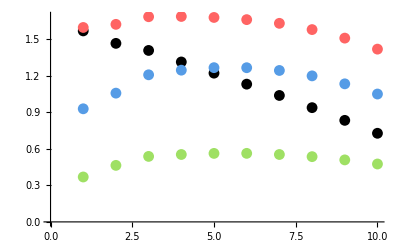

{48.1431,15.3626,19.337,11.1098}

{22.7765,43.9369,13.1889,11.596}

Nominal simulation excursion for hip, knee, ankle, tmt 3D

{59.4549,93.3723,71.2077,31.6929}

Nominal simulation excursion for hip, knee, ankle, tmt 4D

{15.8768,66.5722,66.0983,21.416}

```mathematica
colorsmod=colors;
colorsmod[[4]]=Transparent;

femRETexcDataXY=Thread[{angData,femRETexcData}];
tibRETexcDataXY=Thread[{angData,tibRETexcData}];
tarRETexcDataXY=Thread[{angData,tarRETexcData}];
pftRETexcDataXY=Thread[{angData,pftRETexcData}];

femADDexcDataXY=Thread[{angData,femADDexcData}];
tibADDexcDataXY=Thread[{angData,tibADDexcData}];
tarADDexcDataXY=Thread[{angData,tarADDexcData}];
pftADDexcDataXY=Thread[{angData,pftADDexcData}];

dashthickness=0.01;
pointsize=0.02;
lineStyles1=Thread[{PointSize[pointsize],colorsmod}];
(*lineStyles2=Thread[{Dashing[0.02],Thickness[dashthickness],colorsmod}];*)
lineStyles2=Thread[{PointSize[pointsize],colorsmod}];
lineStyles3=Thread[{PointSize[pointsize*0.6],{White,White,White}}];

(*
plotPitch=Show[
ListPlot[{femRETexcDataXY,tibRETexcDataXY,tarRETexcDataXY},PlotStyle->lineStyles1,BaseStyle->style,PlotRange->{All,{0,160}},AxesStyle->axStyle],
(*ListLinePlot[{femRETexcDataXY,tibRETexcDataXY,tarRETexcDataXY},PlotStyle->colors],*)
ListPlot[{femADDexcDataXY,tibADDexcDataXY,tarADDexcDataXY},PlotStyle->lineStyles2],
ListPlot[{femADDexcDataXY,tibADDexcDataXY,tarADDexcDataXY},PlotStyle->lineStyles3]
]*)
(*plotYaw=Show[

(*ListLinePlot[{femRETexcDataXY,tibRETexcDataXY,tarRETexcDataXY},PlotStyle->colors],*)
ListPlot[{femADDexcDataXY,tibADDexcDataXY,tarADDexcDataXY},PlotStyle->lineStyles2,BaseStyle->style,PlotRange->{All,{-1,160}},AxesStyle->axStyle],
ListPlot[{femADDexcDataXY,tibADDexcDataXY,tarADDexcDataXY},PlotStyle->lineStyles3],
ListPlot[{femRETexcDataXY,tibRETexcDataXY,tarRETexcDataXY},PlotStyle->lineStyles1]
]*)

plotPitchInit=Show[
ListPlot[vcomAngleData,PlotStyle->Black,BaseStyle->style],ListLinePlot[{{0,60},{47.5,60}},PlotStyle->{Black,Dashed}],ListLinePlot[{{47.5,0},{47.5,60}},PlotStyle->{Gray,Dashed}]];


angle3dDATA={hipexcData,kneexcData,ankexcData,tmtexcData};
angle4dDATA={hipexc4dData,kneexc4dData,ankexc4dData,tmtexc4dData};

(*--For ranges of 3D angles----*)
ListPlot[angle3dDATA,PlotStyle->colors]
1/Degree Table[Max[angle3dDATA[[i]]]-Min[angle3dDATA[[i]]],{i,1,4}]
1/Degree Table[Max[angle4dDATA[[i]]]-Min[angle4dDATA[[i]]],{i,1,4}]



exc3dNominal=1/Degree angle3dDATA[[;;,7]];(*3d excersions for hip, knee, ank, tmt for nominal case*)
exc4dNominal=1/Degree angle4dDATA[[;;,7]];(*4d excersions for hip, knee, ank, tmt for nominal case*)

"Nominal simulation excursion for hip, knee, ankle, tmt 3D"
exc3dNominal
"Nominal simulation excursion for hip, knee, ankle, tmt 4D"
exc4dNominal
```

```mathematica
(*save figures as well as information on notebook used to make the figs*)
nbname=(NotebookFileName[]//FileNameSplit)[[-1]];
info="Figures created by "<>nbname;

(*---- for target vary figure---*)
SetDirectory[setpathfigpanel]
Export["targetVary_pitch.pdf",plotPitch];
Export["targetVary_yaw.pdf",plotYaw];
Export["targetVary.txt",info];
ResetDirectory[]
```

/Users/chrisrichards/Desktop/FrogWork/FrogPubs/frogSlerp/figs/panels

/Users/chrisrichards/Desktop/FrogWork/FrogPubs/frogSlerp/simData

```mathematica
nbname=(NotebookFileName[]//FileNameSplit)[[-1]];
info="Figures created by "<>nbname;
(*--- for init vary figure-----*)
SetDirectory[setpathfigpanel]

Export["initVary_plot.pdf",plotPitchInit];
Export["initVary_stick01.gif",stickPlotsInit[[1]],"TransparentColor"->White];
Export["initVary_stick02.gif",stickPlotsInit[[2]],"TransparentColor"->White];
Export["initVary_stick03.gif",stickPlotsInit[[3]],"TransparentColor"->White];
Export["initVary.txt",info];
ResetDirectory[]
```

/Users/chrisrichards/Desktop/FrogWork/FrogPubs/frogSlerp/figs/panels

/Users/chrisrichards/Desktop/FrogWork/FrogPubs/frogSlerp/simData